```mathematica
opencldirectory="/home/chris/Programming/GPU/opencl3/";
```

## Helper

```mathematica
NotebookEvaluate[opencldirectory<>"DetectPeriodTools2.wl"]
NotebookEvaluate[opencldirectory<>"build.wl"]
```

```mathematica
GPUStructureSearch[{20, {2, 1}, 2}]
```

{151,187,189,221,635,889,15903}

#### Utility

```mathematica
Clear[ProgressMap]
ProgressMap[f_, l_List]:=Module[{stdout=PrintTemporary[""], len=Length[l], begin=TimeObject[], cur, avg,eta, tmp, cont=True, out, i=0},
out=ConstantArray[0, len];
While[cont,
i++;
out[[i]]=f[l[[i]]];
NotebookDelete[stdout];
cur=TimeObject[];avg=(cur-begin)/i;eta=begin+len*avg;stdout=PrintTemporary["Step "<>ToString[i]<>"/"<>ToString[len]<>" ("<>ToString[N[100*i/len]]<>"% complete, Avg Time "<>ToString[QuantityMagnitude[avg,"Seconds"]]<>" seconds per elem, ETA "<>DateString[eta, "DateTimeShort"]<>") ", Button["Stop", cont=False]]; 
If[i>=len, cont=False];
];
out[[;;i]]
]
ProgressMap[f_, l_Integer]:=ProgressMap[f, ConstantArray[0, l]]
```

#### Rule Generation

```mathematica
Clear[GoodRuleCondition, GoodTotalisticRuleCondition, RandomGoodRules, RandomGoodTotalisticRules];

GoodRuleCondition[ K_, R_][rule_]:=If[Length[Last[CellularAutomaton[{rule, K, R},{RandomInteger[K-1,100],0},100]]]>150,False,With[{l=Join[Table[Length[StripZeros[CellularAutomaton[{rule,K, R},{RandomInteger[K-1,100],0},{{{100}}}]]],10], Table[Length[StripZeros[CellularAutomaton[{rule, K, R},{RandomInteger[K-1,20],0},{{{100}}}]]],10]]},Mean[l]<100&&Min[l]==0&&Max[l]>0]];

GoodTotalisticRuleCondition[ K_, R_][rule_]:=If[Length[Last[CellularAutomaton[{rule, {K, 1}, R},{RandomInteger[K-1,100],0},100]]]>150,False,With[{l=Join[Table[Length[StripZeros[CellularAutomaton[{rule, {K, 1}, R},{RandomInteger[K-1,100],0},{{{100}}}]]],10], Table[Length[StripZeros[CellularAutomaton[{rule, {K, 1}, R},{RandomInteger[K-1,20],0},{{{100}}}]]],20]]},Mean[l]<100&&Min[l]==0&&Max[l]>0]];

RandomGoodRules[n_, K_:2, R_:1]:={#, K, R}&/@ParallelSelect[Union@ParallelTable[rca[{K,R},"Quiescent"->True,"Type"->"Symmetric"]["RuleNumber"], n], GoodRuleCondition[K, R]]

RandomGoodTotalisticRules[n_, K_:2, R_:1]:={#, {K, 1}, R}&/@ParallelSelect[Union@ParallelTable[rca[{K,R},"Quiescent"->True,"Type"->"Totalistic"]["TotalisticCode"], n], GoodTotalisticRuleCondition[K, R]]
```

#### Checking and Cleanup

```mathematica
Clear[DedupRuleAndRes]
DedupRuleAndRes[{rule_, res_}]:={rule, SortBy[DedupSame[Join@@ParallelMap[init|->DetectPeriod[rule, init], res]], "Canonical"]}
```

```mathematica
Clear[NonTrivialMetric];
NonTrivialMetric[{rule_, res_}]:=Which[
Length[res]==1&&res[[1, "Canonical"]]<16, False, 
AnyTrue[res, KeyExistsQ[#, "IsGliderGun"]&&#["IsGliderGun"]&], True,
Length[res]>40, False,
True, True
]

Clear[NonTrivialMetricRaw];
NonTrivialMetricRaw[{rule_, res_}]:=Which[
Length[res]==1&&res[[1]]<16, False, 
Length[res]>20, False,
True, True
]
```

#### Visualization

```mathematica
FixInteresting[]:=(interestingRules=Union[interestingRules]; interestingResults=(Last@*Sort)/@Values[GroupBy[interestingResults, First]])
ResetInteresting[]:=(interestingRules={};interestingResults={};)

ResetInteresting[]
```

```mathematica
Clear[DecentRunLength]
DecentRunLength[res_, default_]:=Round@Min[If[KeyExistsQ[res, "Period"], 2.2* res["Period"]+30, default], 500]

Clear[DecentRunLengthRaw];
DecentRunLengthRaw[rule_, res_, default_]:=Round@Min[With[{k=AnalyzeRule[rule]["Colors"]},{p=Length[FindRepeatDeterministicByStripZeros[CellularAutomaton[rule, {IntegerDigits[res, k], 0}, default]]]}, If[p!=0, 2.2*p+30, default]], 500]
```

```mathematica
Clear[DisplayRuleResult, DisplayRuleResultRaw]

DisplayRuleResult[rule_, results_, resultSteps_:200, maxNum_:50]:=With[
{k=AnalyzeRule[rule]["Colors"]},Pane[{
Button["Add", AppendTo[interestingRules, rule]; AppendTo[interestingResults, {rule, results}]],
Labeled[ArrayPlot[CellularAutomaton[rule, {RandomInteger[{0, k-1}, 100], 0}, 100]],ClickToCopy[rule]], Row[Table[
Labeled[ArrayPlot[CellularAutomaton[rule, {IntegerDigits[init["Canonical"], k], 0}, DecentRunLength[init, resultSteps]]], ClickToCopy[init["Canonical"], init]]
, {init, results[[;;UpTo[maxNum]]]}], Spacer[1]]
}, 100000]]

DisplayRuleResultRaw[rule_, results_, resultSteps_:200, maxNum_:50]:=With[
{k=AnalyzeRule[rule]["Colors"]},Pane[{
Button["Add", AppendTo[interestingRules, rule]; AppendTo[interestingResults, {rule, results}]],
Labeled[ArrayPlot[CellularAutomaton[rule, {RandomInteger[{0, k-1}, 100], 0}, 100]],ClickToCopy[rule]], Row[Table[
Labeled[ArrayPlot[CellularAutomaton[rule, {IntegerDigits[init, k], 0}, DecentRunLengthRaw[rule, init, resultSteps]]], ClickToCopy[init]]
, {init, results[[;;UpTo[maxNum]]]}], Spacer[1]]
}, 100000]]
```

```mathematica
Clear[DisplayRuleResults]

(* resultdisplayoffset=1;
DisplayRuleResults[ress_, raw_:True, numToShow_:50,resultSteps_:200, maxNum_:50]:=(resultdisplayoffset=1;FixInteresting[];Dynamic[Column[Join[
ParallelTable[
If[raw, DisplayRuleResultRaw, DisplayRuleResult][ress[[i, 1]], ress[[i, 2]], resultSteps, maxNum], {i, resultdisplayoffset, Min[resultdisplayoffset+numToShow-1, Length[ress]]}
], 
If[
resultdisplayoffset+numToShow<Length[ress], {{
"Too many results to show, so they have been truncated.", Button["See More",resultdisplayoffset+=numToShow]
}}, {{"You've seen all results. ", Button["Close", resultdisplayoffset=Length[ress]+1; NotebookDelete[EvaluationCell[]]]}}]]], None, TrackedSymbols:>{resultdisplayoffset}]) *)

DisplayRuleResults[ress_, raw_:True, numToShow_:50,resultSteps_:200, maxNum_:50]:=(FixInteresting[];Column[
ParallelTable[If[raw, DisplayRuleResultRaw, DisplayRuleResult][i[[1]], i[[2]], resultSteps, maxNum], {i, ress}]])
```

```mathematica
VisualizeInterestingResults[steps_:100]:=Column@ParallelTable[DisplayRuleResult@@i, {i, interestingResults}]
```

```mathematica
Clear[VisualizeSingleResult];
VisualizeSingleResult[rule_List, init_List, steps_Integer:100,ops:OptionsPattern[ArrayPlot]]:=ArrayPlot[RunCA[rule, init, steps], {ops}]

VisualizeSingleResult[rule_List, init_Integer, steps_Integer:100,ops:OptionsPattern[ArrayPlot]]:=VisualizeSingleResult[rule, IntegerDigits[init, AnalyzeRule[rule]["Colors"]], steps, {ops}]

VisualizeSingleResult[init_Association, steps_Integer:100,ops:OptionsPattern[ArrayPlot]]:=VisualizeSingleResult[init["Rule"], init["Original"], steps, {ops}]
```

#### Running

```mathematica
Clear[FullStructureSearchRaw, FullStructureSearch];
FullStructureSearchRaw[rules_, min_:0, max_:1000000, timeout_:1000]:=Module[
{ress,nontrivial},
FixInteresting[];

(* Prep memoization in a parallel manner *)
ParallelMap[AnalyzeRule, rules];

ress=ProgressMap[rule|->{rule, GPUStructureSearch[rule, min, max, timeout]}, rules];
ress=Select[ress, ListQ@*Last];
Print[Length[ress]," rules searched with results: ",Iconize[ress]];

nontrivial=ParallelSelect[ress, NonTrivialMetricRaw];
If[Length[nontrivial]<10, nontrivial=ress];
Print[Length[nontrivial], " nontrivial results: ", Iconize[nontrivial]];

DisplayRuleResults[nontrivial]
]

FullStructureSearch[rules_, min_:0, max_:1000000, timeout_:1000]:=Module[
{ress, ressDeduped, nontrivial},
FixInteresting[];

(* Prep memoization in a parallel manner *)
ParallelMap[AnalyzeRule, rules];

ress=ProgressMap[rule|->{rule, GPUStructureSearch[rule, min, max, timeout]}, rules];
ress=Select[ress, ListQ@*Last];
Print[Length[ress]," rules searched with results: ",Iconize[ress]];

(* ressDeduped=ParallelSelect[ress, Length[Last[#]]<50&]; *);
ressDeduped=Function[{rule, res}, If[Length[res]<100, {rule, res}, {rule,Union[Sort[ Join[res[[;;50]], RandomChoice[res, 50]]]]}]]@@@ress;

ressDeduped=Map[DedupRuleAndRes, ressDeduped];
Print[Total[Length/@ress], " total results deduped to ",Total[Length/@ressDeduped], " ", Iconize[ressDeduped]];

nontrivial=ParallelSelect[ressDeduped, NonTrivialMetric];
If[Length[nontrivial]<10, nontrivial=ressDeduped];
Print[Length[nontrivial], " nontrivial results: ", Iconize[nontrivial]];

 nontrivial=ressDeduped;

DisplayRuleResults[nontrivial, False]
]

FullStructureSearchQuiet[rules_, min_:0, max_:1000000, timeout_:1000]:=Module[
{ress, ressDeduped, nontrivial},
FixInteresting[];

(* Prep memoization in a parallel manner *)
ParallelMap[AnalyzeRule, rules];

ress=ProgressMap[rule|->{rule, GPUStructureSearch[rule, min, max, timeout]}, rules];
ress=Select[ress, ListQ@*Last];

ressDeduped=Map[DedupRuleAndRes, ress];

ressDeduped
]
```

## Mutating Identity Rule

```mathematica
Clear[PointMutateChoice]
PointMutateChoice[rule_, n_:1]:=Module[{ar=AnalyzeRule[rule], k, r, rn, o, out},
k=ar["Colors"];
r=ar["Radius"];
rn=ar["Number"];
o=IntegerDigits[rn, k, k^(2r+1)];
Do[o[[i]]=RandomInteger[{0, k-1}], {i, RandomChoice[Range[k^(2r+1)-1], n]}];
out=FromDigits[o, k];
{out, k, r}
]

Clear[PointMutateSample]
PointMutateSample[rule_, n_:1]:=Module[{ar=AnalyzeRule[rule], k, r, rn, o, out},
k=ar["Colors"];
r=ar["Radius"];
rn=ar["Number"];
o=IntegerDigits[rn, k, k^(2r+1)];
Do[o[[i]]=RandomChoice[DeleteCases[Range[0, k-1], o[[i]]]], {i, RandomSample[Range[k^(2r+1)-1], n]}];
out=FromDigits[o, k];
{out, k, r}
]
```

```mathematica
k=2;r=2;
identityRule={FromDigits[Tuples[Reverse@Range[0, k-1], 2r+1][[All, r+1]], k], k, r};
```

```mathematica
Union[Table[PointMutateChoiceSym[identityRule, 2], 100]]
```

{{1894838496,2,2},{1894838512,2,2},{2968547568,2,2},{2985324792,2,2},{3102765296,2,2},{3497046256,2,2},{3497062624,2,2},{3497062640,2,2},{3773952114,2,2},{3774149232,2,2},{4038115504,2,2},{4038119664,2,2},{4040225008,2,2},{4041269392,2,2},{4041273552,2,2},{4042305776,2,2},{4042318000,2,2},{4042322144,2,2},{4042322160,2,2},{4042322420,2,2},{4042387698,2,2},{4042453232,2,2},{4042584816,2,2},{4042585840,2,2},{4054896888,2,2},{4057002232,2,2},{4059083000,2,2},{4059099384,2,2},{4059230456,2,2},{4074303728,2,2},{4076400880,2,2},{4109433056,2,2},{4109433072,2,2},{4176539888,2,2}}

```mathematica
AArrayPlot[#, RandomInteger[2^30], Frame->False]&/@Table[PointMutateChoiceSym[identityRule, i], {i, 50}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
AArrayPlot[#, RandomInteger[2^100]]&/@Table[PointMutateChoiceSym[identityRule, i], {i, 50}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
AArrayPlot[#, RandomInteger[2^100]]&/@
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ArrayPlot[CellularAutomaton[identityRule, {RandomInteger[{0, k-1}, 100], 0}, 100]]
```

-Graphics-

```mathematica
ArrayPlot[CellularAutomaton[PointMutateSample[identityRule, 10], {RandomInteger[{0, k-1}, 100], 0}, 100]]
```

-Graphics-

```mathematica
data1=Quiet[ProgressMap[mutations|->N[Mean[ParallelTable[
TimeConstrained[
Boole[AnyTrue[DetectPeriod[PointMutateChoice[identityRule, mutations], RandomInteger[2^20]], #IsGliderGun&]],
10, Nothing], 100]]], Range[0, 50]]]
data2=Quiet[ProgressMap[mutations|->N[Mean[ParallelTable[
TimeConstrained[
Boole[AnyTrue[DetectPeriod[PointMutateSample[identityRule, mutations], RandomInteger[2^20]], #IsGliderGun&]],
10, Nothing], 100]]], Range[0, 50]]]
```

{0.,0.06,0.08,0.16,0.17,0.23,0.18,0.32,0.29,0.31,0.333333,0.393939,0.36,0.53,0.464646,0.43299,0.505155,0.520833,0.556701,0.526316,0.616162,0.574468,0.5,0.6,0.723404,0.542553,0.55102,0.574468,0.580645,0.606383,0.613636,0.6,0.608696,0.617021,0.550562,0.72043,0.622222,0.629213,0.611111,0.662921,0.619565,0.565217,0.604396,0.608696,0.651163,0.704545,0.62069,0.652174,0.689655,0.588235,0.644444}

{0.,0.11,0.17,0.23,0.38,0.454545,0.42,0.474747,0.57732,0.619565,0.551724,0.648936,0.647059,0.617978,0.722892,0.630952,0.714286,0.729412,0.738095,0.821429,0.857143,0.906977,0.875,0.932584,0.913978,0.989247,0.979167,1.,1.,1.,1.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

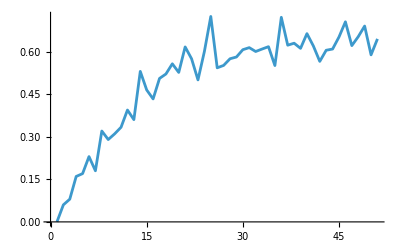

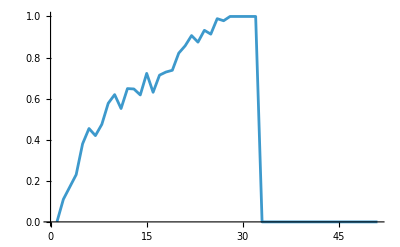

```mathematica
ListPlot[data1, Joined->True]
ListPlot[data2, Joined->True]
```

```mathematica
DetectPeriod
```

## Research Question: How many mutations are necessary for life to emerge?

```mathematica
Clear[PointMutateChoiceSym]
PointMutateChoiceSym[rule_,n_:1]:=Module[{ar=AnalyzeRule[rule],k,r,rn,o,out,m,mirrorPos,canonicals,chosen},k=ar["Colors"];
r=ar["Radius"];
rn=ar["Number"];
m=k^(2 r+1);
o=IntegerDigits[rn,k,m];
mirrorPos[i_]:=m-FromDigits[Reverse[IntegerDigits[m-i,k,2 r+1]],k];
canonicals=Select[Range[m-1],#<=mirrorPos[#]&];
chosen=RandomChoice[canonicals,n];
Do[With[{val=RandomInteger[{0,k-1}],mir=mirrorPos[i]},o[[i]]=val;
o[[mir]]=val],{i,chosen}];
out=FromDigits[o,k];
{out,k,r}]
```

```mathematica
Clear[SymmetricRuleQ]
SymmetricRuleQ[n_,k_,r_]:=Module[{m,o,mirrorPos},m=k^(2 r+1);
o=IntegerDigits[n,k,m];
mirrorPos[i_]:=m-FromDigits[Reverse[IntegerDigits[m-i,k,2 r+1]],k];
AllTrue[Range[m],o[[#]]==o[[mirrorPos[#]]]&]]
```

{4042322160,2,2}

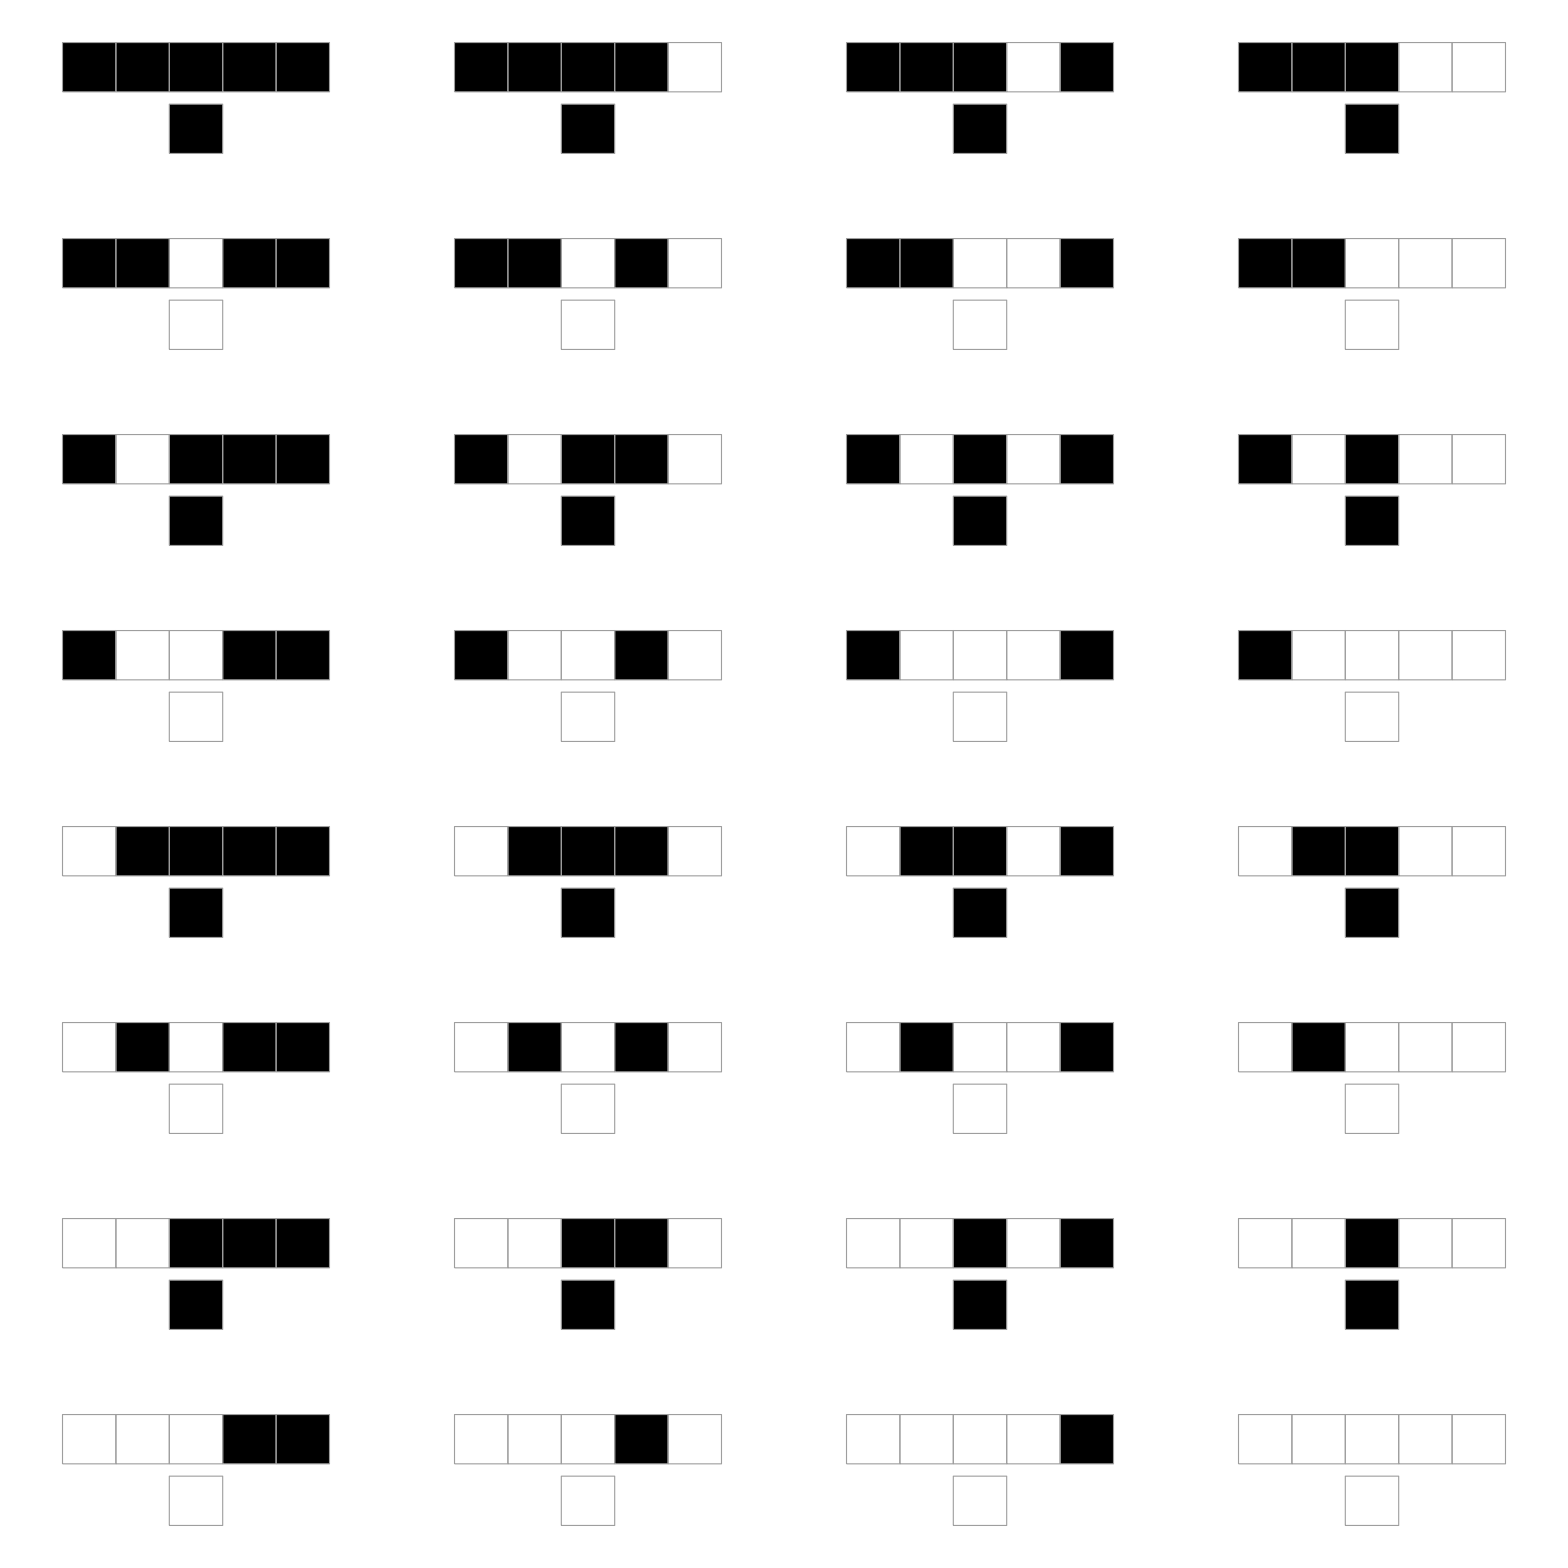

64

31

{1,7,33,119,353,903,2029,4064,7285,11678,16799,22086,26599,29641,30766,29916,27107,22871,18210,13420,9420,6072,3632,2010,1006,457,168,70,21,3,1}

286747

```mathematica
k=2;r=2;
identityRule={FromDigits[Tuples[Reverse@Range[0, k-1], 2r+1][[All, r+1]], k], k, r}
RulePlot[CellularAutomaton[identityRule]]

maxmut=2*(k^(2r+1))

(* Generate many mutations *)
rules=Union[Join@@ParallelTable[Union@Table[PointMutateChoiceSym[identityRule, mutations], 10000], {mutations, 0, maxmut}]];

(* Group by mutation distance *)
rules=Values[Join[AssociationMap[{}&, Range[0, maxmut]],GroupBy[rules, HammingDistance[IntegerDigits[#[[1]], k, k^(2r+1)], IntegerDigits[identityRule[[1]], k, k^(2r+1)]]&]]]//.{x__, {}}->{x};

Length[rules]
Length/@rules
Length[Join@@rules]
```

```mathematica
RulePlot[CellularAutomaton[{4042322160,2,2}]]
```

-Graphics-

```mathematica
Clear[ThereExistsInitWhichDoesntGrowInfinitelyOrDie]
ThereExistsInitWhichDoesntGrowInfinitelyOrDie[rule_, numChecks_:50]:=AnyTrue[Range[numChecks],seed|->(SeedRandom[seed];With[{
l=Length[StripZeros[
RunCA[rule, RandomInteger[k^50], {{{100}}}]
]]},
l>0&&l<=100
])]
```

```mathematica
Clear[ThereExistsInitWhichGrowsInfinitely]
ThereExistsInitWhichGrowsInfinitely[rule_, tries_:50]:=AnyTrue[RandomInteger[k^20, tries], AnyTrue[DetectPeriod[rule, #], #IsGliderGun&]&]

Clear[ThereExistsInitWhichGrowsInfinitelyGPU]
ThereExistsInitWhichGrowsInfinitelyGPU[rule_, max_:100000]:=AnyTrue[GPUStructureSearch[rule, 0, max], AnyTrue[DetectPeriod[rule, #], #IsGliderGun&]&]
```

```mathematica
$RecursionLimit=65536;
```

```mathematica
ProgressMap[i|->Mean@N@ParallelTable[
TimeConstrained[
Boole[
ThereExistsInitWhichDoesntGrowInfinitelyOrDie[rule]&&ThereExistsInitWhichGrowsInfinitely[rule]
],30, Nothing],
{rule,RandomSample[rules[[i]], UpTo[100]]}], Range[Length[rules]]]
```

{0.,0.,0.030303,0.04,0.08,0.11,0.05,0.13,0.13,0.163265,0.11,0.07,0.04,0.0606061,0.010101,0.06,0.03,0.03,0.01,0.03,0.02,0.01,0.01,0.01,0.01,0.,0.,0.,0.,0.,0.}

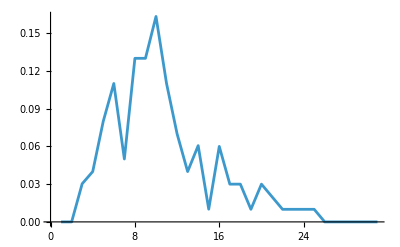

```mathematica
ListPlot[, Joined->True]
```

## Mutating Zero Rule

{0,2,2}

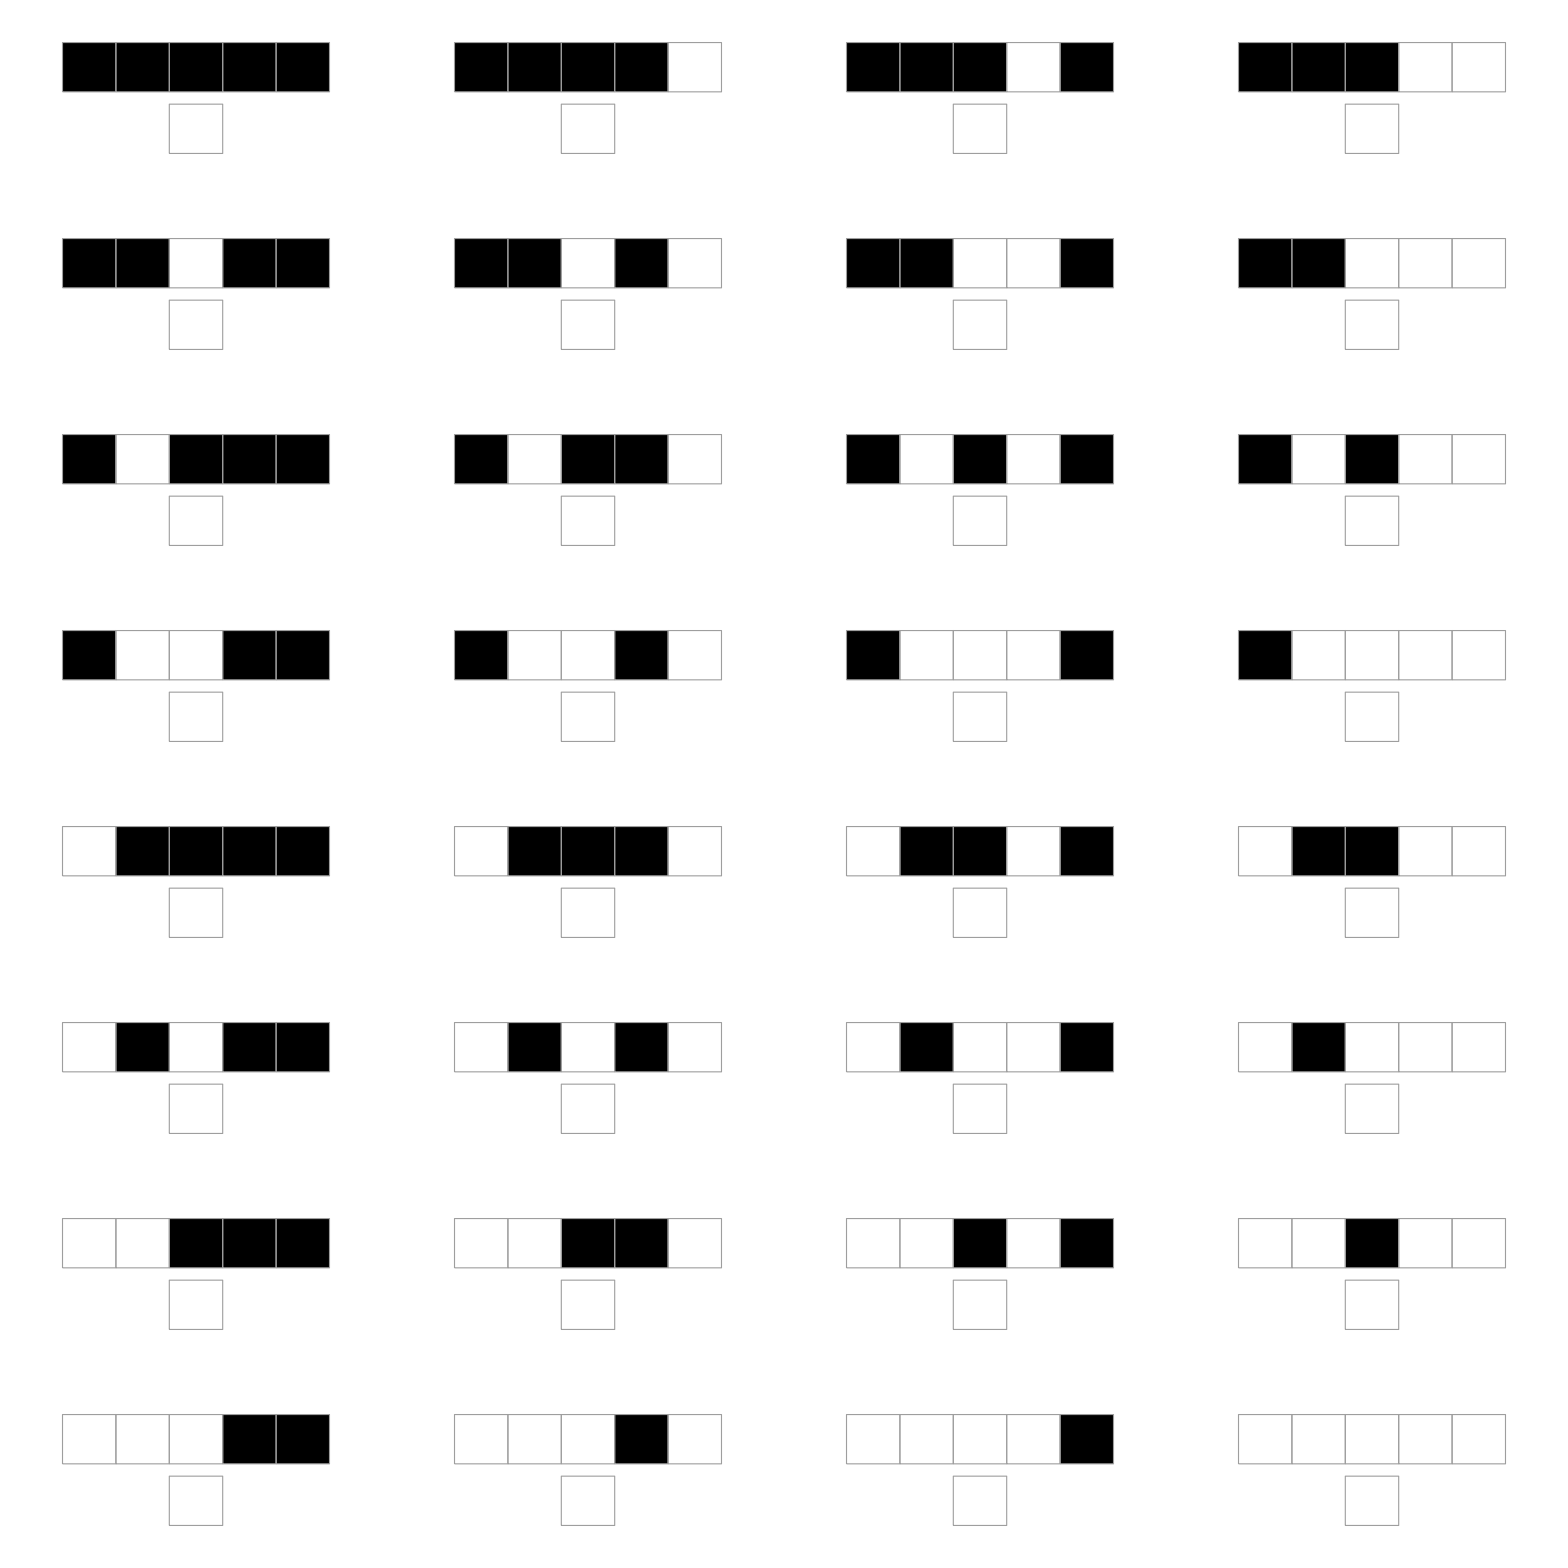

64

31

{1,7,33,119,353,903,2029,4057,7284,11670,16787,22071,26634,29636,30741,29673,26877,22948,18232,13571,9432,6044,3549,1951,954,413,221,68,27,5,1}

286291

```mathematica
k=2;r=2;
identityRule={0, k, r}
RulePlot[CellularAutomaton[identityRule]]

maxmut=2*(k^(2r+1))

(* Generate many mutations *)
rules=Union[Join@@ParallelTable[Union@Table[PointMutateChoiceSym[identityRule, mutations], 10000], {mutations, 0, maxmut}]];

(* Group by mutation distance *)
rules=Values[Join[AssociationMap[{}&, Range[0, maxmut]],GroupBy[rules, HammingDistance[IntegerDigits[#[[1]], k, k^(2r+1)], IntegerDigits[identityRule[[1]], k, k^(2r+1)]]&]]]//.{x__, {}}->{x};

Length[rules]
Length/@rules
Length[Join@@rules]
```

```mathematica
ProgressMap[i|->Mean@N@ParallelTable[
TimeConstrained[
Boole[
ThereExistsInitWhichDoesntGrowInfinitelyOrDie[rule]&&ThereExistsInitWhichGrowsInfinitely[rule]
],10, Nothing],
{rule,RandomSample[rules[[i]], UpTo[50]]}], Range[Length[rules]]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.04,0.02,0.1,0.06,0.0408163,0.06,0.,0.,0.0612245,0.04,0.04,0.06,0.02,0.02,0.04,0.02,0.02,0.,0.,0.,0.,0.,0.}

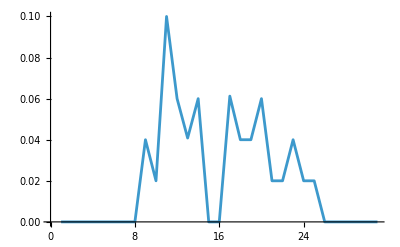

```mathematica
ListPlot[, Joined->True]
```

## Topology of Living Rules

```mathematica
Select[Range[0, 255, 2], SymmetricRuleQ[#, 2, 1]&]
```

{0,4,18,22,32,36,50,54,72,76,90,94,104,108,122,126,128,132,146,150,160,164,178,182,200,204,218,222,232,236,250,254}

```mathematica
edges=Union[Sort/@Join@@ParallelTable[i<->#&/@Union[Table[PointMutateChoiceSym[{i, 2, 1}, 1][[1]], 100]], {i, }]]/.x_<->x_->Nothing;
```

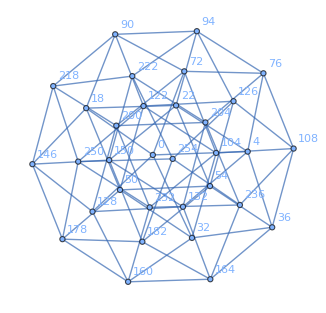

```mathematica
Graph[, edges, VertexLabels->Automatic]
```

```mathematica
vd=ParallelSelect[, ThereExistsInitWhichGrowsInfinitely[{#, 2, 1}]&]
```

{18,22,50,54,90,94,122,126,146,150,178,182,218,222,250,254}

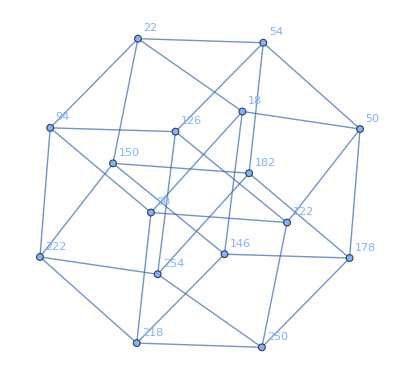

```mathematica
VertexDelete[Graph[, edges, VertexLabels->Automatic], Complement[, vd]]
```

#### Diversity of Phenotypes Generated

```mathematica
Clear[DiversityMap]
DiversityMap[rules_, steps_:1000, k_:2, len_:8]:=ReverseSort[Association[ParallelMap[ rule|->rule->Length[Union[Join@@Table[Union[FromDigits[#, k]&/@Union@Partition[row, len, 1]], {row, Rest@RunCA[rule, RandomInteger[k^50], steps]}]]], rules]]]
```

```mathematica
assoc=DiversityMap[vd]
Keys[assoc]
```

<|150→256,90→254,22→225,54→161,122→154,182→146,94→141,18→119,146→112,126→108,50→71,178→69,250→62,218→53,222→47,254→22|>

{150,90,22,54,122,182,94,18,146,126,50,178,250,218,222,254}

```mathematica
ClickToCopy[AArrayPlot[{#, 2, 1}, RandomInteger[2^20], 300], #]&/@Keys[assoc]
```

{-Graphics-150,-Graphics-90,-Graphics-22,-Graphics-54,-Graphics-122,-Graphics-182,-Graphics-94,-Graphics-18,-Graphics-146,-Graphics-126,-Graphics-50,-Graphics-178,-Graphics-250,-Graphics-218,-Graphics-222,-Graphics-254}

## Density of Nonzero Necessary for Life

```mathematica
segments=Range[0, 32];
rules=ParallelTable[{#, 2, 2}&/@Union@Table[FromDigits[RandomSample[Table[Boole[i<=threshold], {i, 32}]], 2], 30], {threshold, segments}];
```

```mathematica
t1=ProgressMap[i|->Mean@N@ParallelTable[
TimeConstrained[
Boole[
ThereExistsInitWhichDoesntGrowInfinitelyOrDie[rule]
],5, Nothing],
{rule,rules[[i]]}], Range[Length[rules]]]
t2=ProgressMap[i|->Mean@N@ParallelTable[
TimeConstrained[
Boole[ThereExistsInitWhichGrowsInfinitely[rule]
],5, Nothing],
{rule,rules[[i]]}], Range[Length[rules]]]
t3=ProgressMap[i|->Mean@N@ParallelTable[
TimeConstrained[
Boole[
ThereExistsInitWhichDoesntGrowInfinitelyOrDie[rule]&&ThereExistsInitWhichGrowsInfinitely[rule]
],5, Nothing],
{rule,rules[[i]]}], Range[Length[rules]]]
```

{0.,0.166667,0.433333,0.433333,0.4,0.566667,0.633333,0.6,0.6,0.6,0.533333,0.466667,0.533333,0.533333,0.333333,0.333333,0.3,0.3,0.166667,0.2,0.266667,0.266667,0.466667,0.5,0.433333,0.466667,0.6,0.566667,0.566667,0.366667,0.321429,0.222222,0.}

{0.,0.,0.,0.,0.037037,0.037037,0.0714286,0.130435,0.12,0.208333,0.26087,0.666667,0.571429,0.5,0.681818,0.772727,0.8,0.875,0.962963,1.,0.962963,0.961538,0.769231,0.964286,0.689655,0.724138,0.586207,0.5,0.517241,0.413793,0.0714286,0.111111,0.}

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.172414,0.142857,0.115385,0.0689655,0.137931,0.103448,0.172414,0.103448,0.2,0.233333,0.266667,0.310345,0.433333,0.3,0.266667,0.344828,0.172414,0.266667,0.166667,0.107143,0.111111,0.}

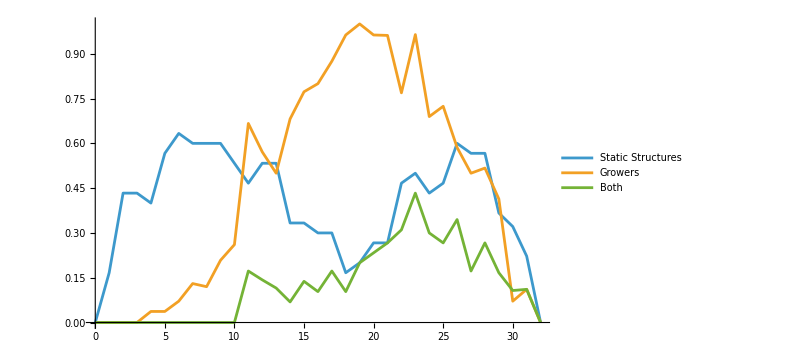

```mathematica
ListPlot[Thread[{segments,#}]&/@{t1, t2, t3}, Joined->True, PlotLegends->{"Static Structures", "Growers", "Both"}]
```

## Identity Mutations 2

```mathematica
$RecursionLimit=2^16;
```

```mathematica
k=2;r=2;
identityRule={FromDigits[Tuples[Reverse@Range[0, k-1], 2r+1][[All, r+1]], k], k, r}

maxmut=2*(k^(2r+1))

(* Generate many mutations *)
rules=Union[Join@@ParallelTable[Union@Table[PointMutateChoiceSym[identityRule, mutations], 1000], {mutations, 0, maxmut}]];

(* Group by mutation distance *)
rules=Values[Join[AssociationMap[{}&, Range[0, maxmut]],GroupBy[rules, HammingDistance[IntegerDigits[#[[1]], k, k^(2r+1)], IntegerDigits[identityRule[[1]], k, k^(2r+1)]]&]]]//.{x__, {}}->{x};

Length[rules]
Length/@rules
Length[Join@@rules]
```

{4042322160,2,2}

64

30

{1,7,33,119,331,750,1312,1962,2591,3149,3762,4331,4521,4732,4578,4104,3663,3153,2307,1610,1146,763,428,233,108,61,24,4,2,1}

49786

```mathematica
ResourceFunction["MonitorProgress"]@Map[Mean[N@Values[DiversityMap[RandomSample[#, UpTo[50]]]]]&,rules]
```

{34.,39.2857,40.9394,42.86,49.92,50.96,62.26,71.56,82.52,99.86,99.18,117.48,142.36,151.42,144.9,177.88,179.48,181.8,194.78,183.26,184.22,185.44,191.48,178.72,156.3,140.82,145.14,128.02,106.714,95.1667}

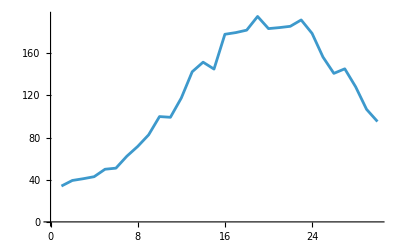

```mathematica
ListLinePlot[]
```

```mathematica
t1=ProgressMap[i|->Mean@N@ParallelTable[
TimeConstrained[
Boole[
ThereExistsInitWhichDoesntGrowInfinitelyOrDie[rule]
],10, Nothing],
{rule,RandomSample[rules[[i]], UpTo[30]]}], Range[Length[rules]]]
t2=ProgressMap[i|->Mean@N@ParallelTable[
TimeConstrained[
Boole[ThereExistsInitWhichGrowsInfinitely[rule]
],10, Nothing],
{rule,RandomSample[rules[[i]], UpTo[30]]}], Range[Length[rules]]]
t3=ProgressMap[i|->Mean@N@ParallelTable[
TimeConstrained[
Boole[
ThereExistsInitWhichDoesntGrowInfinitelyOrDie[rule]&&ThereExistsInitWhichGrowsInfinitely[rule]
],10, Nothing],
{rule,RandomSample[rules[[i]], UpTo[30]]}], Range[Length[rules]]]
```

{1.,1.,0.966667,0.933333,0.833333,0.866667,0.833333,0.8,0.7,0.633333,0.466667,0.466667,0.366667,0.333333,0.4,0.3,0.3,0.266667,0.133333,0.0666667,0.1,0.0666667,0.0333333,0.,0.,0.0666667,0.0333333,0.,0.,0.}

{0.,0.,0.0666667,0.133333,0.166667,0.233333,0.233333,0.3,0.344828,0.392857,0.52,0.5,0.538462,0.347826,0.4,0.75,0.588235,0.666667,0.882353,0.823529,0.866667,0.75,0.913043,0.909091,0.92,1.,1.,1.,1.,1.}

{0.,0.,0.,0.1,0.0333333,0.0333333,0.0333333,0.1,0.166667,0.0666667,0.0666667,0.1,0.0344828,0.137931,0.0333333,0.0344828,0.,0.0666667,0.0333333,0.0689655,0.0666667,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
ListPlot[Thread[{Range[Length[#]], #}]&/@{t1, t2, t3}, Joined->True, PlotLegends->{"Static Structures", "Growers", "Both"}]
```

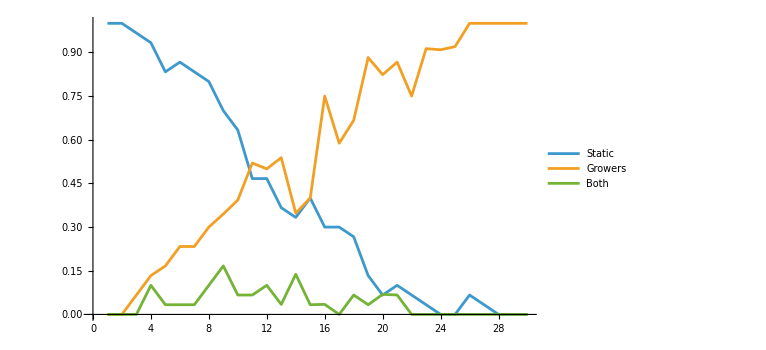

Include proportion of die-out rules / structures?

## new

```mathematica
k=2;r=2;
antiIdentityRule={FromDigits[1-Tuples[Reverse@Range[0, k-1], 2r+1][[All, r+1]], k]-1, k, r}
```

{252645134,2,2}

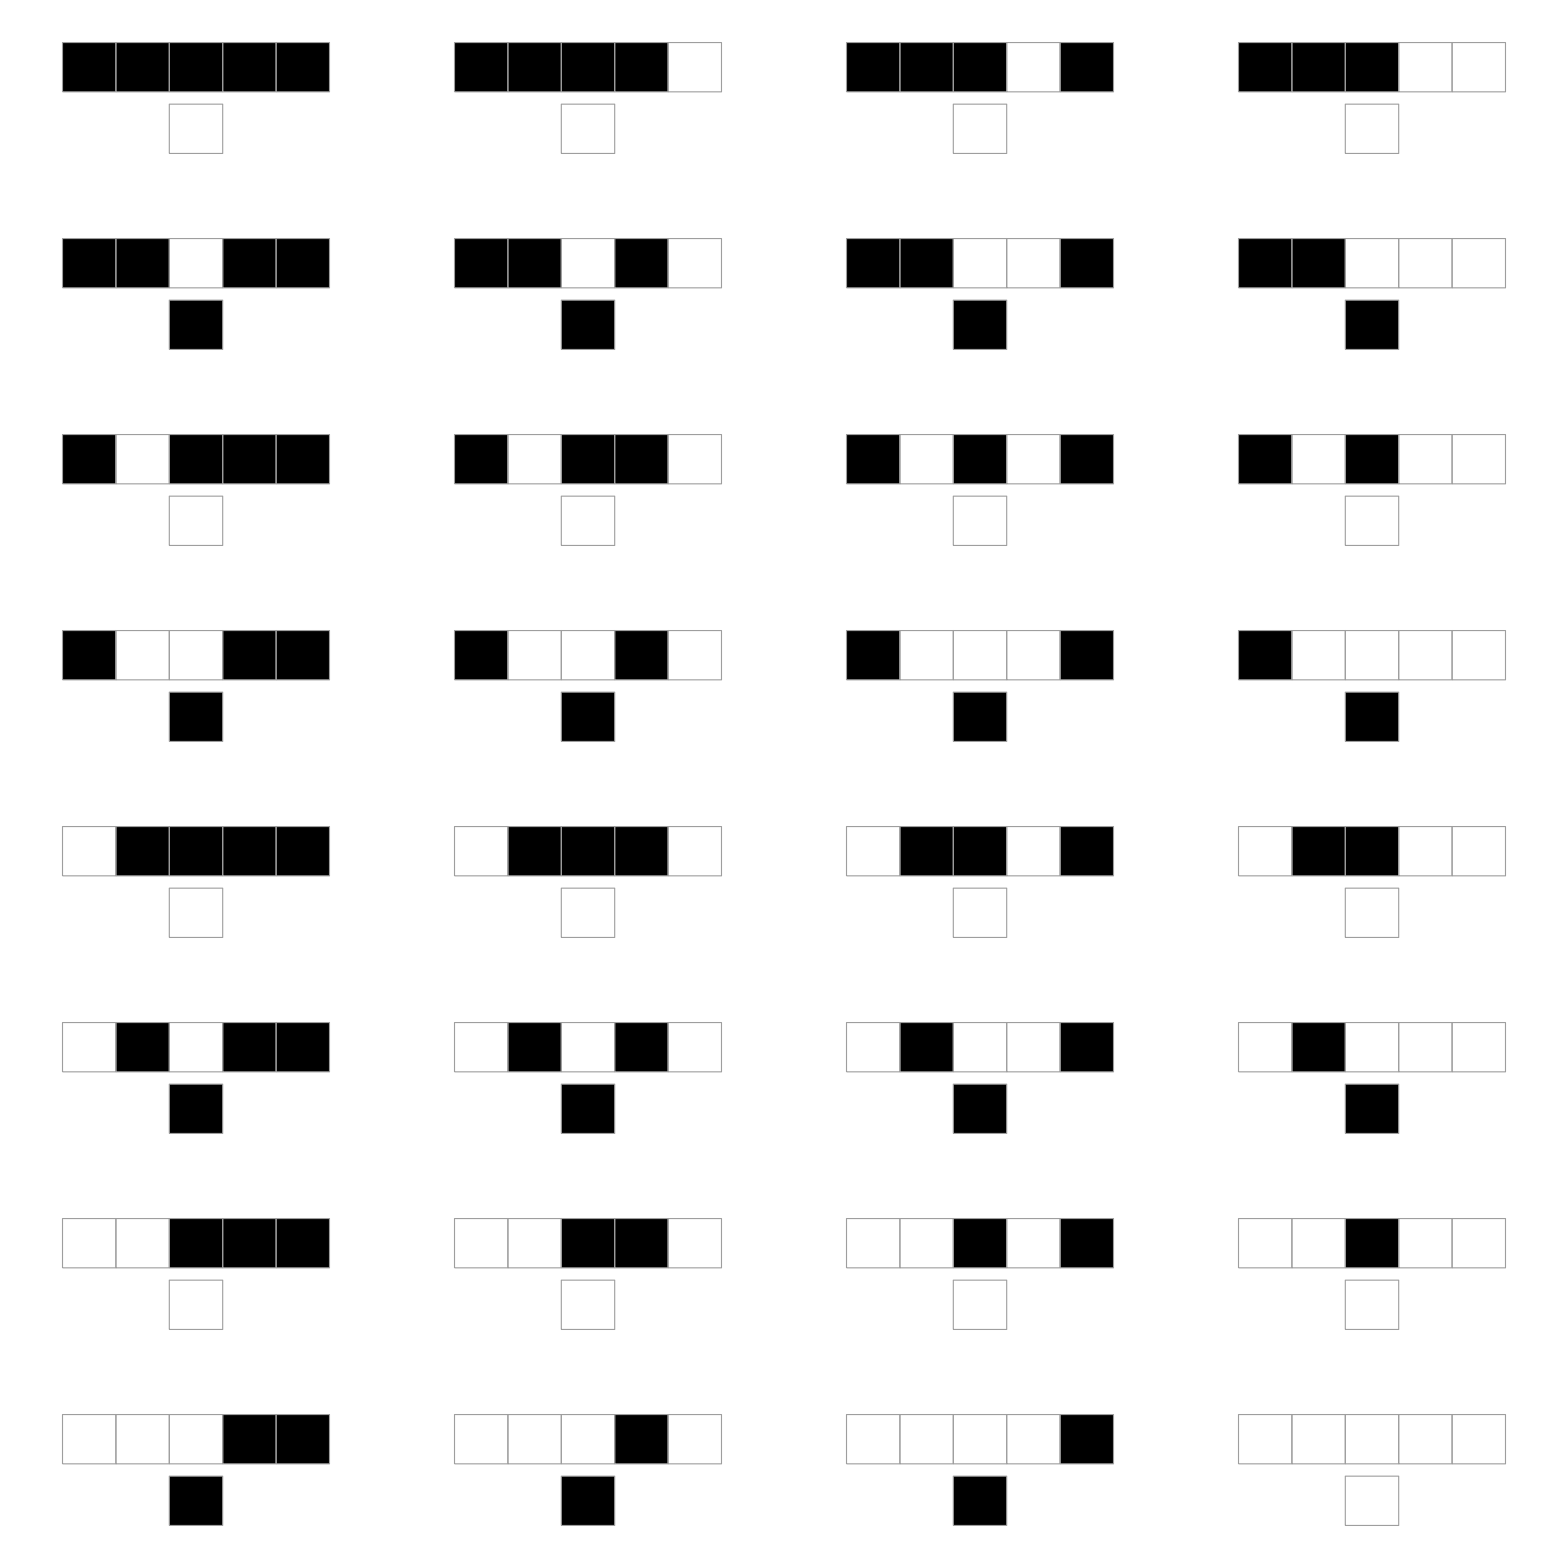

```mathematica
RulePlot[CellularAutomaton[antiIdentityRule]]
```

```mathematica
AArrayPlot[antiIdentityRule, RandomInteger[2^20], 10]
```

-Graphics-

```mathematica
GPUStructureSearch[{1329, {3, 1}, 1}, 0, 10000000]//AbsoluteTiming
```

```mathematica
DedupSame[Join@@ParallelMap[DetectPeriod[{20, {2, 1}, 2}, #]&,Range[1, 1000000, 2]]]
```

{<|Rule→{20,{2,1},2},Canonical→189,Original→189,IsGliderGun→False,MaxDepth→0,MaxSteps→200,Period→1,Shift→0,LowestDepth→20|>,<|Rule→{20,{2,1},2},Canonical→635,Original→635,IsGliderGun→False,MaxDepth→0,MaxSteps→200,Period→1,Shift→1,LowestDepth→20|>,<|Rule→{20,{2,1},2},Canonical→151,Original→151,IsGliderGun→False,MaxDepth→0,MaxSteps→200,Period→2,Shift→0,LowestDepth→20|>,<|Rule→{20,{2,1},2},Canonical→595703,Original→595703,IsGliderGun→False,MaxDepth→0,MaxSteps→200,Period→4,Shift→0,LowestDepth→20|>,<|Rule→{20,{2,1},2},Canonical→610999,Original→610999,IsGliderGun→False,MaxDepth→0,MaxSteps→200,Period→4,Shift→0,LowestDepth→20|>,<|Rule→{20,{2,1},2},Canonical→187,Original→187,IsGliderGun→False,MaxDepth→0,MaxSteps→200,Period→9,Shift→1,LowestDepth→20|>,<|Rule→{20,{2,1},2},Canonical→15903,Original→195,IsGliderGun→False,MaxDepth→0,MaxSteps→200,Period→22,Shift→0,LowestDepth→20|>,<|Rule→{20,{2,1},2},Canonical→125231,Original→125231,IsGliderGun→False,MaxDepth→0,MaxSteps→200,Period→38,Shift→0,LowestDepth→20|>}

```mathematica
AArrayPlot[{20, {2, 1}, 2}, #, 200]&/@[[All, "Original"]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
AArrayPlot[{1329, {3, 1}, 1}, #, 2000]&/@RandomSample[[[2]], 10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Frequency of Structures as r={1, 2, 3, 4...}?

## Strict Self-Replication

```mathematica
Clear[InitSelfReplicates]
InitSelfReplicates[rule_, init_]:=AnyTrue[RunCA[rule, init, 100], row|->MatchQ[StripZeros[row], {Sequence@@init, __, Sequence@@init}]]

Clear[InitSelfReplicatesStrict]
InitSelfReplicatesStrict[rule_, init_]:=AnyTrue[RunCA[rule, init, 100], row|->MatchQ[StripZeros[row], {Sequence@@init, Repeated[0, {8, Infinity}], Sequence@@init}]]

Clear[InitSelfReplicatesSortaStrict]
InitSelfReplicatesSortaStrict[rule_, init_]:=AnyTrue[RunCA[rule, init, 100], row|->MatchQ[StripZeros[row], {Sequence@@init, 0.., Sequence@@init, 0.., Sequence@@init, 0.., Sequence@@init}]]
```

```mathematica
InitSelfReplicates[{20, {2, 1}, 2}, 189]
```

False

```mathematica
InitSelfReplicates[{2404331018,2,2}, {1, 1, 0, 1, 1}]
```

True

```mathematica
InitSelfReplicatesStrict[{2404331018,2,2}, {1, 1, 0, 1, 1, 0, 0, 1, 1, 0, 1, 1}]
```

False

```mathematica
Clear[Try]
Try[f_, elems_]:=Module[{o=$Failed, i=1}, While[(o=f[elems[[i]]])===$Failed&&i<Length[elems], i++]; o]

Clear[SelfReplicates]
SelfReplicates[rule_]:=Try[If[InitSelfReplicates[rule,  IntegerDigits[#, 2]], #, $Failed]&,Range[1, 100, 2]]/.$Failed->None

Clear[SelfReplicatesStrict]
SelfReplicatesStrict[rule_]:=Try[If[InitSelfReplicatesStrict[rule, IntegerDigits[#, 2]], #, $Failed]&,Range[1, 100, 2]]/.$Failed->None

Clear[SelfReplicatesSortaStrict]
SelfReplicatesSortaStrict[rule_]:=Try[If[InitSelfReplicatesSortaStrict[rule,  IntegerDigits[#, 2]], #, $Failed]&,Range[1, 100, 2]]/.$Failed->None
```

```mathematica
SelfReplicatesStrict[{20, {2, 1}, 2}]
```

None

```mathematica
SelfReplicates[{2404331018,2,2}]
```

1

```mathematica
SelfReplicates[{1329, {3, 1}, 1}]
SelfReplicatesStrict[{1329, {3, 1}, 1}]
```

1

None

```mathematica
SelfReplicatesStrict[{2, {2, 1}, 2}]
```

1

```mathematica
k=2;r=2;
identityRule={FromDigits[Tuples[Reverse@Range[0, k-1], 2r+1][[All, r+1]], k], k, r}

maxmut=2*(k^(2r+1))

(* Generate many mutations *)
rules=Union[Join@@ParallelTable[Union@Table[PointMutateChoiceSym[identityRule, mutations], 1000], {mutations, 0, maxmut}]];

(* Group by mutation distance *)
rules=Values[Join[AssociationMap[{}&, Range[0, maxmut]],GroupBy[rules, HammingDistance[IntegerDigits[#[[1]], k, k^(2r+1)], IntegerDigits[identityRule[[1]], k, k^(2r+1)]]&]]]//.{x__, {}}->{x};

Length[rules]
Length/@rules
Length[Join@@rules]
```

{4042322160,2,2}

64

31

{1,7,33,115,341,742,1303,1980,2617,3268,3854,4382,4689,4735,4556,4131,3593,3031,2302,1663,1126,726,401,201,104,47,25,9,4,0,2}

49988

```mathematica
xs=Range[1, Length[rules], 1];

t1=ProgressMap[i|->{i, Mean@N@ParallelTable[
TimeConstrained[Boole[SelfReplicates[rule]=!=None],10, Nothing],
{rule,RandomSample[rules[[i]], UpTo[100]]}]}, xs]

t2=ProgressMap[i|->{i, Mean@N@ParallelTable[
TimeConstrained[Boole[SelfReplicatesStrict[rule]=!=None],10, Nothing],
{rule,RandomSample[rules[[i]], UpTo[100]]}]}, xs]
```

{{1,0.},{2,0.},{3,0.0909091},{4,0.18},{5,0.29},{6,0.46},{7,0.44},{8,0.53},{9,0.52},{10,0.59},{11,0.54},{12,0.72},{13,0.79},{14,0.76},{15,0.88},{16,0.88},{17,0.87},{18,0.87},{19,0.89},{20,0.92},{21,0.87},{22,0.96},{23,1.},{24,0.99},{25,0.99},{26,1.},{27,1.},{28,1.},{29,1.},{30,Mean[{}]},{31,1.}}

{{1,0.},{2,0.},{3,0.},{4,0.02},{5,0.02},{6,0.01},{7,0.09},{8,0.1},{9,0.15},{10,0.2},{11,0.26},{12,0.16},{13,0.18},{14,0.23},{15,0.17},{16,0.27},{17,0.32},{18,0.38},{19,0.36},{20,0.4},{21,0.42},{22,0.42},{23,0.4},{24,0.34},{25,0.29},{26,0.212766},{27,0.28},{28,0.111111},{29,0.},{30,Mean[{}]},{31,0.}}

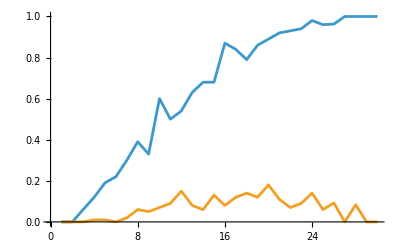

```mathematica
ListPlot[{t1, t2}, Joined->True]
```

```mathematica
somerules=Catenate[#[[;;UpTo[10]]]&/@rules];
t4=ParallelTable[With[{o=SelfReplicatesStrict[rule]}, If[o===None, Nothing, {rule, o}]], {rule, somerules}];
```

```mathematica
t4
```

{{{7435362,2,2},1},{{1134690,2,2},1},{{4272194,2,2},1},{{4288854,2,2},1},{{5334050,2,2},1},{{3216758,2,2},1},{{3495522,2,2},1},{{6317316,2,2},1},{{1135974,2,2},1},{{1119590,2,2},1},{{2168150,2,2},1},{{3347814,2,2},1},{{3212582,2,2},1},{{4547350,2,2},1},{{6645526,2,2},1},{{82182,2,2},1},{{2430806,2,2},1},{{6629142,2,2},1},{{83206,2,2},1},{{18171434,2,2},1},{{21374748,2,2},1},{{34341636,2,2},1},{{37553958,2,2},1},{{51189338,2,2},1},{{52036908,2,2},1},{{67439366,2,2},1},{{101523286,2,2},1},{{103615254,2,2},1},{{119410492,2,2},1},{{201658134,2,2},1},{{253628204,2,2},1}}

```mathematica
AArrayPlot[#1, #2]&@@@t4
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
AArrayPlot[{6317316,2,2}, RandomInteger[2^20], 500]
```

-Graphics-

```mathematica
k=4;r=2;
identityRule={FromDigits[Tuples[Reverse@Range[0, k-1], 2r+1][[All, r+1]], k], k, r}

maxmut=2*(k^(2r+1))

(* Generate many mutations *)
rules=Union[Join@@ParallelTable[Union@Table[PointMutateChoiceSym[identityRule, mutations], 100], {mutations, 0, maxmut}]];

(* Group by mutation distance *)
rules=Values[Join[AssociationMap[{}&, Range[0, maxmut]],GroupBy[rules, HammingDistance[IntegerDigits[#[[1]], k, k^(2r+1)], IntegerDigits[identityRule[[1]], k, k^(2r+1)]]&]]]//.{x__, {}}->{x};

Length[rules]
Length/@rules
Length[Join@@rules]
```

{32317006068802877525281122402017510238181165926339315299185042876825208323580671664344962074786061410964063680945324545055162046185368430251480158567721600633726077715640008885004981388765614582084733982403219353971790523578595912504671087259139622340386832934226946065986944224181775151899409659870287905860136548723767147276127838131136606012652265263674205848136724467539022950197658563482766389632443642499615342589575089471150008496072014727307997065683073286299681477351024833221896712227556661657972540902621262298458495132170943732408759572377061071141429348250890684570201867695832596887384175967717703024640,4,2}

2048

816

{1,13,117,21,95,39,107,51,86,49,103,71,61,70,99,73,57,61,77,64,79,61,59,78,82,84,75,69,72,77,63,73,71,78,85,77,72,78,76,78,75,92,82,65,64,78,76,75,73,70,77,64,78,73,65,87,74,74,90,78,83,82,85,69,69,79,75,80,72,76,98,77,72,70,76,87,91,65,84,67,95,66,71,73,82,91,70,78,88,68,73,84,84,86,88,82,81,75,73,77,87,93,76,91,82,85,84,83,82,98,81,83,94,79,79,74,75,91,97,86,86,71,65,80,81,100,95,93,78,106,79,96,74,85,80,84,77,78,83,86,84,87,78,85,88,96,102,75,82,90,87,80,89,100,84,89,89,91,83,90,83,91,92,94,93,102,108,101,91,81,85,70,96,91,92,95,85,79,94,97,78,97,104,94,115,84,107,100,79,92,91,105,101,90,97,76,98,82,87,92,119,83,99,99,107,91,102,86,81,112,91,109,103,119,119,129,95,88,78,76,103,89,98,97,98,79,105,101,89,111,111,93,103,113,92,96,103,117,108,97,97,119,123,98,103,88,93,103,109,116,105,100,107,109,94,123,100,111,129,107,121,98,109,92,122,88,114,107,101,119,105,109,96,107,111,103,116,95,95,117,123,124,103,113,105,123,96,121,109,111,110,127,129,111,113,111,135,130,97,113,137,124,120,103,121,113,123,127,117,126,130,117,126,111,130,126,109,119,128,85,130,120,116,112,149,110,104,124,118,142,127,119,118,123,115,149,122,132,132,104,131,124,123,145,130,123,148,126,160,118,118,108,129,106,134,152,137,145,121,125,151,120,127,136,141,125,139,137,150,131,157,143,127,139,141,121,161,136,162,124,136,164,136,141,147,127,143,173,132,155,161,132,161,135,140,154,153,135,145,152,142,150,146,164,131,137,130,167,140,161,164,160,146,168,131,168,151,128,156,138,152,166,162,157,159,196,144,180,158,144,160,159,144,172,162,159,168,165,145,163,168,181,177,174,172,171,175,161,173,165,165,164,161,174,182,184,190,169,164,176,178,168,179,178,185,191,180,185,161,185,169,202,178,202,188,181,196,185,184,198,181,198,222,171,182,202,181,189,184,181,204,202,198,216,196,196,212,221,195,208,203,211,188,206,213,193,192,213,196,195,201,232,204,211,203,228,229,221,203,212,200,241,226,234,227,245,236,200,239,229,221,259,229,243,228,248,237,231,252,228,243,245,233,233,240,256,254,251,247,256,269,239,222,245,258,240,278,246,279,276,273,279,281,250,259,262,256,270,292,264,286,319,295,282,315,279,269,290,293,286,304,309,306,270,309,289,329,305,331,319,295,332,320,287,299,335,315,306,356,331,327,357,327,316,330,317,334,378,322,332,383,361,356,318,383,391,392,386,369,350,382,403,399,359,386,379,369,393,406,405,428,409,406,406,416,417,432,426,445,387,469,449,412,426,454,433,423,482,429,501,472,473,431,497,461,525,500,527,474,487,492,567,554,533,576,530,577,584,576,578,567,644,635,595,634,631,604,622,663,667,665,634,720,711,705,659,698,707,743,783,731,715,761,815,778,821,817,900,853,859,879,882,942,941,920,915,953,966,978,1046,977,997,1002,1080,1063,1015,1088,1148,1118,1086,1137,1190,1120,1196,1215,1156,1244,1186,1218,1276,1224,1265,1239,1219,1188,1187,1197,1184,1107,1107,1187,1127,1106,1052,1020,1093,1014,949,995,945,972,853,845,852,782,806,747,683,661,618,626,592,566,527,478,453,441,370,365,348,329,325,293,260,259,204,210,172,168,153,140,132,114,93,84,90,71,72,69,47,45,52,28,33,31,18,34,11,17,12,18,11,3,9,5,6,6,4,3,1,1,0,1,0,3,1}

204760

```mathematica
xs=Range[1, Length[rules], 1];

t1=ProgressMap[i|->{i, Mean@N@ParallelTable[
TimeConstrained[Boole[SelfReplicates[rule]=!=None],10, Nothing],
{rule,RandomSample[rules[[i]], UpTo[30]]}]}, xs]

t2=ProgressMap[i|->{i, Mean@N@ParallelTable[
TimeConstrained[Boole[SelfReplicatesStrict[rule]=!=None],10, Nothing],
{rule,RandomSample[rules[[i]], UpTo[30]]}]}, xs]
```

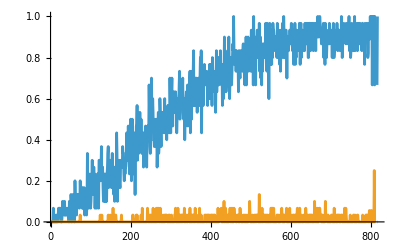

```mathematica
ListPlot[{t1, t2}, Joined->True]
```

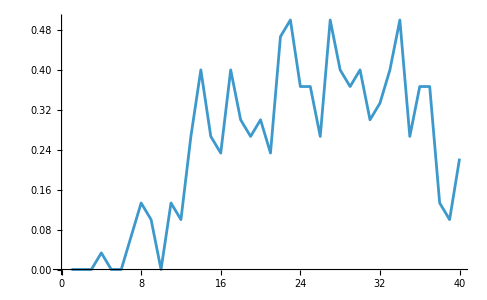

```mathematica
ListPlot[Total/@Partition[t2[[All, 2]], 20], Joined->True]
```

```mathematica
k=2;r=3;
identityRule={FromDigits[Tuples[Reverse@Range[0, k-1], 2r+1][[All, r+1]], k], k, r}

maxmut=2*(k^(2r+1))

(* Generate many mutations *)
rules=Union[Join@@ParallelTable[Union@Table[PointMutateChoiceSym[identityRule, mutations], 100], {mutations, 0, maxmut}]];

(* Group by mutation distance *)
rules=Values[Join[AssociationMap[{}&, Range[0, maxmut]],GroupBy[rules, HammingDistance[IntegerDigits[#[[1]], k, k^(2r+1)], IntegerDigits[identityRule[[1]], k, k^(2r+1)]]&]]]//.{x__, {}}->{x};

Length[rules]
Length/@rules
Length[Join@@rules]
```

{338958311018522360492699998064329424640,2,3}

256

90

{1,13,66,78,160,74,139,111,147,117,167,110,167,147,154,150,161,156,168,152,158,193,181,173,191,191,192,198,213,193,226,238,217,254,261,271,280,272,340,332,369,345,402,414,455,495,520,546,596,606,628,652,697,688,769,717,756,757,726,740,701,716,660,641,580,486,443,413,346,289,275,185,152,160,108,80,68,47,33,19,16,15,7,9,5,3,1,0,0,2}

25350

```mathematica
rulesmin=RandomSample[#, UpTo[100]]&/@rules;
rulesmap=ParallelTable[AssociationMap[rule|->Boole[SelfReplicatesStrict[rule]=!=None], ruless], {ruless, rulesmin}];
```

```mathematica
xs=Range[1, Length[rules], 1];

t1=ProgressMap[i|->{i, Mean@N@ParallelTable[
TimeConstrained[Boole[SelfReplicates[rule]=!=None],10, Nothing],
{rule,RandomSample[rules[[i]], UpTo[80]]}]}, xs]

t2=ProgressMap[i|->{i, Mean@N@ParallelTable[
TimeConstrained[Boole[SelfReplicatesStrict[rule]=!=None],10, Nothing],
{rule,RandomSample[rules[[i]], UpTo[80]]}]}, xs]
```

{{1,0.},{2,0.},{3,0.05},{4,0.0571429},{5,0.0375},{6,0.125},{7,0.15},{8,0.175},{9,0.225},{10,0.2},{11,0.2},{12,0.2},{13,0.25},{14,0.3375},{15,0.2625},{16,0.325},{17,0.25},{18,0.45},{19,0.3},{20,0.4},{21,0.375},{22,0.4375},{23,0.525},{24,0.4625},{25,0.5},{26,0.5375},{27,0.5},{28,0.5375},{29,0.575},{30,0.5375},{31,0.6125},{32,0.525},{33,0.625},{34,0.6375},{35,0.5625},{36,0.525},{37,0.6125},{38,0.6125},{39,0.775},{40,0.7125},{41,0.6},{42,0.775},{43,0.7},{44,0.7875},{45,0.7625},{46,0.6875},{47,0.8375},{48,0.7125},{49,0.7625},{50,0.8125},{51,0.8},{52,0.825},{53,0.875},{54,0.75},{55,0.7875},{56,0.825},{57,0.8375},{58,0.8875},{59,0.875},{60,0.75},{61,0.8375},{62,0.8875},{63,0.9},{64,0.85},{65,0.9},{66,0.875},{67,0.8875},{68,0.8875},{69,0.9125},{70,0.9125},{71,0.925},{72,0.8875},{73,0.925},{74,0.9625},{75,0.9625},{76,0.9125},{77,0.966102},{78,0.916667},{79,0.9},{80,1.},{81,0.961538},{82,0.933333},{83,1.},{84,1.},{85,0.75},{86,1.},{87,1.},{88,1.},{89,1.},{90,Mean[{}]},{91,1.}}

{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.025},{7,0.},{8,0.025},{9,0.},{10,0.0125},{11,0.},{12,0.0125},{13,0.025},{14,0.0125},{15,0.},{16,0.025},{17,0.0375},{18,0.0125},{19,0.025},{20,0.0125},{21,0.0375},{22,0.0625},{23,0.0625},{24,0.0375},{25,0.05},{26,0.05},{27,0.0625},{28,0.0625},{29,0.0375},{30,0.0875},{31,0.1125},{32,0.05},{33,0.075},{34,0.0875},{35,0.0625},{36,0.05},{37,0.0375},{38,0.075},{39,0.075},{40,0.05},{41,0.0875},{42,0.0875},{43,0.0625},{44,0.075},{45,0.1125},{46,0.0625},{47,0.1625},{48,0.0875},{49,0.1375},{50,0.05},{51,0.1625},{52,0.125},{53,0.05},{54,0.0625},{55,0.0625},{56,0.0625},{57,0.1},{58,0.0875},{59,0.0875},{60,0.05},{61,0.1375},{62,0.0875},{63,0.1125},{64,0.0625},{65,0.1125},{66,0.0375},{67,0.075},{68,0.125},{69,0.1},{70,0.125},{71,0.025},{72,0.0875},{73,0.0125},{74,0.075},{75,0.0875},{76,0.075},{77,0.0169492},{78,0.0416667},{79,0.0333333},{80,0.0588235},{81,0.115385},{82,0.133333},{83,0.0909091},{84,0.},{85,0.},{86,0.},{87,0.},{88,0.},{89,0.},{90,Mean[{}]},{91,1.}}

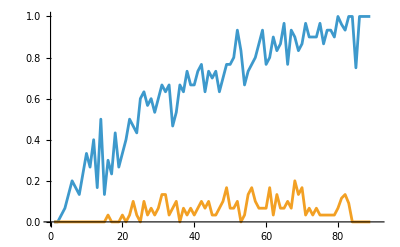

```mathematica
ListPlot[{t1, t2}, Joined->True]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.01,0.01,0.,0.,0.01,0.02,0.02,0.04,0.02,0.01,0.06,0.02,0.,0.07,0.07,0.03,0.05,0.03,0.07,0.02,0.03,0.07,0.05,0.04,0.08,0.07,0.07,0.1,0.06,0.07,0.08,0.15,0.09,0.08,0.09,0.12,0.12,0.1,0.07,0.09,0.09,0.13,0.06,0.09,0.04,0.15,0.07,0.07,0.11,0.09,0.07,0.05,0.13,0.13,0.11,0.13,0.1,0.07,0.07,0.09,0.06,0.09,0.08,0.12,0.05,0.04,0.1375,0.0588235,0.0638298,0.,0.0526316,0.,0.0666667,0.,0.,0.,0.,0.,Mean[{}],Mean[{}],0.}

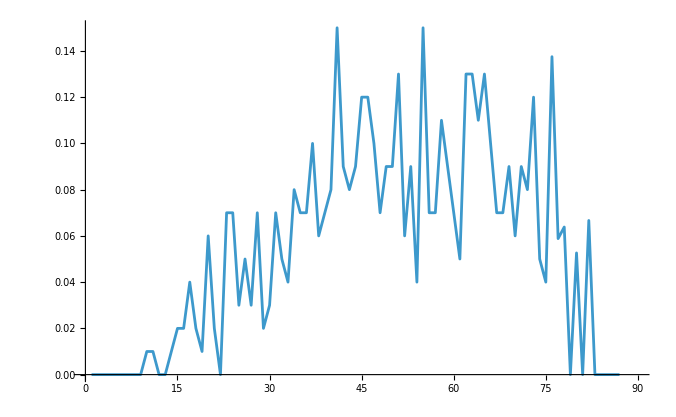

```mathematica
Mean[N@Values[#]]&/@rulesmap
ListLinePlot[%]
```

```mathematica
map=Join@@rulesmap;
```

## new 2

```mathematica
ParallelSelect[RandomSample[Union[Join@@rules], 100],TimeConstrained[ SelfReplicatesSortaStrict[#]=!=None, 5, False]&]
```

{{3906052146,2,2},{520706266,2,2},{1277200644,2,2},{1018498998,2,2},{1002116330,2,2},{685974806,2,2},{3255670338,2,2},{1623701074,2,2},{2387425858,2,2},{3511018122,2,2},{1180696162,2,2},{55260250,2,2},{1758979618,2,2},{2799659554,2,2},{1529644940,2,2},{2371103532,2,2},{549860164,2,2},{3920860266,2,2},{721122678,2,2},{370870710,2,2},{819164662,2,2},{953229474,2,2},{472128452,2,2},{1001083082,2,2},{2506243532,2,2}}

```mathematica
AArrayPlot[#, 1, ImageSize->Medium]&/@{{520706266,2,2}, {721122678,2,2}, {1018498998,2,2}, {3906052146,2,2}}//Column
```

-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
carun=RunCA[{721122678,2,2}, 1, 100];
mask=RunCA[{k^(k^(2r+1))-2, k, r}, 3, 100];
```

```mathematica
ArrayPlot[mask]
```

-Graphics-

```mathematica
0.01*Times@@Dimensions[carun]
```

405.01

```mathematica
Table[ArrayPlot[BitXor[carun[[All, ;;-i]], carun[[All, i;;]]]], {i, 1, 10}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
InitSelfReplicatesNonSerpenski[rule_, init_]:=With[{carun=RunCA[rule, init, 500]},AnyTrue[Range[2, 10],i|->Total[BitXor[carun[[All, ;;-i]], carun[[All, i;;]]], 2]<0.01*Times@@Dimensions[carun]]]
```

```mathematica
SelfReplicatesNonSerpenski[rule_]:=Try[If[InitSelfReplicatesNonSerpenski[rule,#1],#1,$Failed]&,Range[1,100,2]]/. $Failed->None
```

```mathematica
ParallelSelect[RandomSample[Union[Join@@rules], 100],TimeConstrained[ SelfReplicatesNonSerpenski[#]=!=None, 5, False]&]
```

{{4192707226,2,2},{2466780360,2,2},{3941458434,2,2},{2215053842,2,2},{2968679648,2,2},{788151652,2,2},{270812816,2,2},{2982442956,2,2},{476085700,2,2},{4126584748,2,2},{2106710250,2,2},{3558906064,2,2},{1347729136,2,2},{2851500924,2,2},{1888653552,2,2},{2349162326,2,2},{259532840,2,2},{3648057836,2,2},{3035855090,2,2},{2503089400,2,2},{1777398904,2,2},{4108368324,2,2},{3850410332,2,2},{1349972720,2,2},{2996650658,2,2},{2671450622,2,2},{339967170,2,2},{3925079146,2,2},{2490662624,2,2},{4243045058,2,2},{1429265916,2,2},{4143705266,2,2},{303846372,2,2},{342915296,2,2},{3561011408,2,2},{2577238,2,2},{884083124,2,2},{3514299130,2,2},{922566630,2,2},{3325611056,2,2},{3807032660,2,2},{1157943068,2,2},{3629163940,2,2},{1992089312,2,2},{3852590430,2,2},{3770937410,2,2},{1412598960,2,2},{1215756148,2,2},{274936002,2,2},{4104510162,2,2},{1066945704,2,2},{2304798792,2,2},{4009736818,2,2},{1480037106,2,2},{3546084088,2,2},{971338442,2,2},{4241685744,2,2},{1383920628,2,2},{1690347796,2,2},{552805686,2,2},{3591297728,2,2},{2322342676,2,2},{747855206,2,2},{2984534664,2,2},{2451331060,2,2},{1911615996,2,2},{2760138320,2,2},{2059063780,2,2},{3852769864,2,2},{2998620386,2,2},{4091393786,2,2},{3801776160,2,2},{3659367074,2,2},{1756402800,2,2},{1911596216,2,2},{87039096,2,2},{2518243570,2,2},{3889949998,2,2},{4072182000,2,2},{3575879882,2,2}}

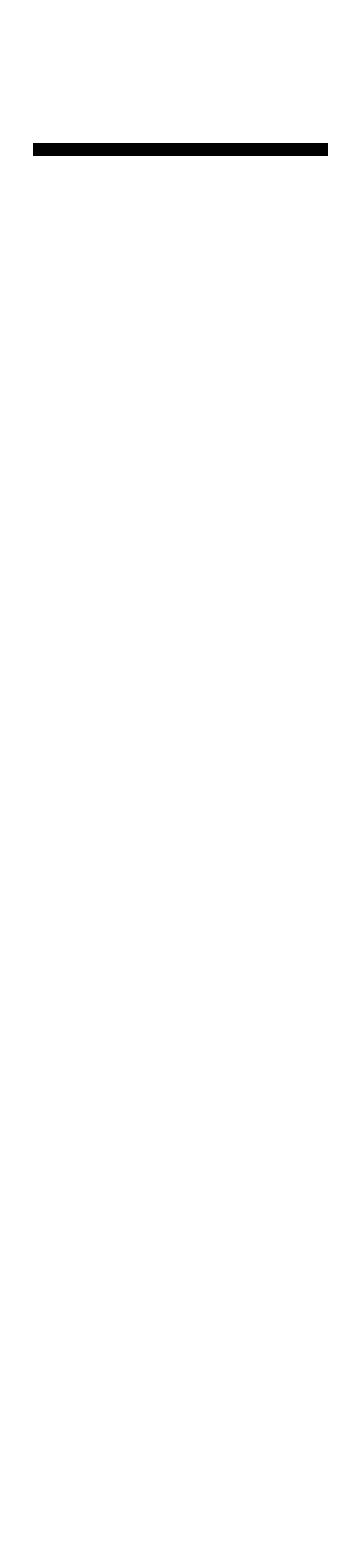
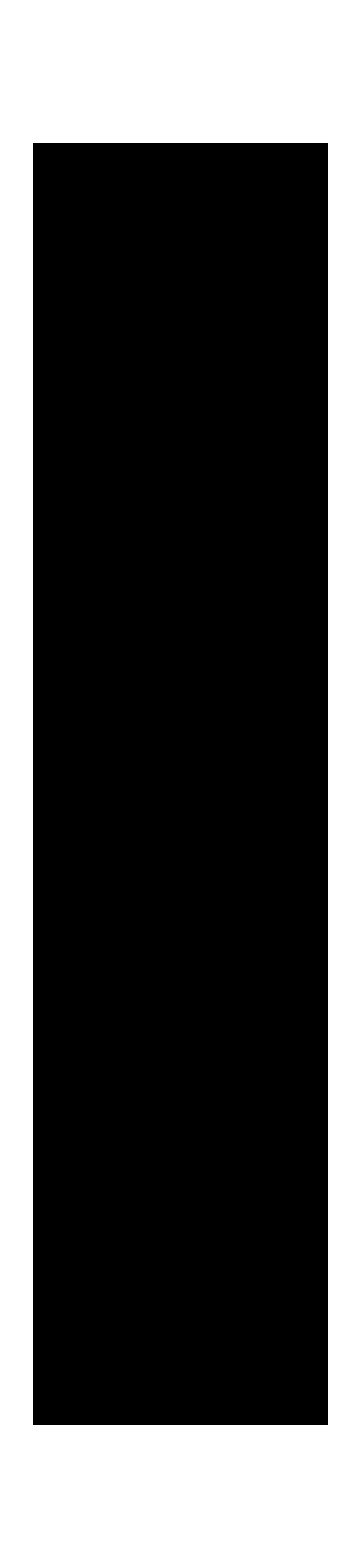
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
AArrayPlot[#, 1, ImageSize->Medium]&/@[[;;UpTo[20]]]
```

```mathematica
thing[rule_, init_]:=SelectFirst[RunCA[rule, init, 100], (row|->MatchQ[StripZeros[row], {Sequence@@init, Repeated[0, {8, Infinity}], Sequence@@init}])->"Index"]
```

```mathematica
rulesample=Union[Join@@rules];
ReverseSortBy[ParallelMap[#->thing[#, {1}]/.(_->Missing["NotFound"])->Nothing&,rulesample], Last]
```

```mathematica
[[3]]
```

{3628245380,2,2}→18

```mathematica
AArrayPlot[{3628245380,2,2}, 1, 3000]
```

-Graphics-

```mathematica
AArrayPlot[#, 1, 300]&/@[[;;UpTo[20], 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
GPUStructureSearch[{1329, {3, 1}, 1}, 0, 1000]
```

{400,9571,22234,22960,525304562024518979}

```mathematica
GPUStructureSearch[{20, {2, 1}, 2}, 0, 2000000000]//AbsoluteTiming
GPUStructureSearch[{20, {2, 1}, 2}, 0, 1000000000]//AbsoluteTiming
```

{23.4438,{151,187,189,221,635,889,15903,125231,595703,610999,624623,14871103,16537415,1461002907,1864495775,22503642597}}

{11.6196,{151,187,189,221,635,889,15903,125231,595703,610999,624623,14871103,16537415,22503642597}}

```mathematica
3.282948-1.863662
```

1.41929

```mathematica
1.863662-1.4192860000000003
```

0.444376

```mathematica
MinimalBooleanForm[]
```

MinimalBooleanForm[]

```mathematica
AnalyzeRule[{20,{2,1},2}]
```

<|Rule→{20,{2,1},2},NormalRule→{1771476584,2,2},Colors→2,Radius→2,Totalistic→True,Number→1771476584,Quiescent→True,Symmetric→True|>

{0,1,1,0,1,0,0,1,1,0,0,1,0,1,1,0,1,0,0,1,0,1,1,0,0,1,1,0,1,0,0,0}

```mathematica
e0=Xor[#1, #2, #3, #4, #5, Or[#1, #2, #3, #4, #5]]
```

(#1||#2||#3||#4||#5)⊻#1⊻#2⊻#3⊻#4⊻#5

```mathematica
RandomInteger[{0, 1}, 256]
```

{0,0,0,1,1,0,1,1,0,1,1,0,1,1,0,0,1,0,0,1,1,1,1,0,0,0,0,0,1,0,1,1,0,1,0,0,1,1,1,1,0,0,0,1,1,0,0,1,0,0,0,0,0,1,0,0,1,0,0,1,0,0,0,0,0,1,1,0,1,0,0,0,1,0,1,1,1,0,0,0,1,0,1,1,1,0,0,1,1,0,0,0,1,1,1,0,1,1,1,0,0,0,0,0,0,1,0,0,1,1,0,1,0,1,1,1,1,1,0,0,1,0,1,0,1,0,0,0,0,1,1,1,0,1,0,1,1,0,1,1,1,0,0,0,1,0,0,0,1,0,0,0,0,0,1,1,1,1,1,1,1,1,1,0,0,1,0,1,1,1,0,0,1,0,0,0,0,1,1,1,1,0,0,1,0,0,0,0,0,1,1,1,1,0,0,0,1,1,1,1,1,0,0,0,1,1,0,0,0,1,0,1,1,0,0,0,0,1,1,0,0,0,1,1,0,1,1,0,0,1,1,0,0,0,1,0,1,1,1,1,1,0,1,0,0,1,1,0,0,1,1,1,0,1,1,1}

```mathematica
FromDigits[%, 2]
```

12404357175556427020932068810772933836971384411120900870961900609759295284855

```mathematica
RepeatedTiming[BooleanMinimize[BooleanFunction[12404357175556427020932068810772933836971384411120900870961900609759295284855], "ANF"][[1]]]
```

{0.000118646,!((#1&&#4)⊻(#1&&#5)⊻(#2&&#4)⊻(#2&&#5)⊻(#2&&#6)⊻(#3&&#4)⊻(#3&&#6)⊻(#3&&#7)⊻(#4&&#6)⊻(#5&&#7)⊻(#5&&#8)⊻(#7&&#8)⊻(#1&&#2&&#3)⊻(#1&&#2&&#4)⊻(#1&&#2&&#5)⊻(#1&&#3&&#5)⊻(#1&&#3&&#6)⊻(#1&&#3&&#8)⊻(#1&&#4&&#5)⊻(#1&&#4&&#8)⊻(#1&&#5&&#6)⊻(#1&&#5&&#8)⊻(#1&&#6&&#8)⊻(#2&&#3&&#4)⊻(#2&&#3&&#5)⊻(#2&&#3&&#7)⊻(#2&&#4&&#5)⊻(#2&&#5&&#6)⊻(#3&&#5&&#8)⊻(#3&&#6&&#8)⊻(#3&&#7&&#8)⊻(#4&&#5&&#6)⊻(#4&&#6&&#8)⊻(#4&&#7&&#8)⊻(#5&&#6&&#7)⊻(#5&&#7&&#8)⊻(#1&&#2&&#3&&#5)⊻(#1&&#2&&#3&&#7)⊻(#1&&#2&&#3&&#8)⊻(#1&&#2&&#4&&#7)⊻(#1&&#2&&#5&&#6)⊻(#1&&#2&&#6&&#7)⊻(#1&&#2&&#7&&#8)⊻(#1&&#3&&#4&&#7)⊻(#1&&#3&&#5&&#6)⊻(#1&&#3&&#5&&#7)⊻(#1&&#3&&#5&&#8)⊻(#1&&#3&&#6&&#7)⊻(#1&&#3&&#6&&#8)⊻(#1&&#3&&#7&&#8)⊻(#1&&#4&&#5&&#6)⊻(#1&&#4&&#5&&#7)⊻(#1&&#4&&#5&&#8)⊻(#1&&#4&&#6&&#7)⊻(#1&&#4&&#6&&#8)⊻(#1&&#4&&#7&&#8)⊻(#1&&#5&&#6&&#8)⊻(#1&&#6&&#7&&#8)⊻(#2&&#3&&#4&&#5)⊻(#2&&#3&&#5&&#6)⊻(#2&&#3&&#5&&#7)⊻(#2&&#3&&#6&&#7)⊻(#2&&#3&&#6&&#8)⊻(#2&&#4&&#5&&#6)⊻(#2&&#4&&#5&&#7)⊻(#2&&#4&&#6&&#7)⊻(#2&&#4&&#6&&#8)⊻(#2&&#4&&#7&&#8)⊻(#2&&#5&&#6&&#8)⊻(#2&&#6&&#7&&#8)⊻(#3&&#4&&#6&&#7)⊻(#3&&#4&&#7&&#8)⊻(#3&&#5&&#6&&#7)⊻(#4&&#5&&#6&&#7)⊻(#4&&#5&&#6&&#8)⊻(#4&&#5&&#7&&#8)⊻(#4&&#6&&#7&&#8)⊻(#1&&#2&&#3&&#4&&#5)⊻(#1&&#2&&#3&&#4&&#8)⊻(#1&&#2&&#3&&#5&&#6)⊻(#1&&#2&&#3&&#5&&#7)⊻(#1&&#2&&#3&&#5&&#8)⊻(#1&&#2&&#3&&#7&&#8)⊻(#1&&#2&&#4&&#5&&#6)⊻(#1&&#2&&#4&&#6&&#7)⊻(#1&&#2&&#4&&#7&&#8)⊻(#1&&#2&&#5&&#6&&#7)⊻(#1&&#2&&#5&&#6&&#8)⊻(#1&&#3&&#4&&#5&&#6)⊻(#1&&#3&&#4&&#5&&#7)⊻(#1&&#3&&#4&&#5&&#8)⊻(#1&&#3&&#4&&#6&&#8)⊻(#1&&#3&&#4&&#7&&#8)⊻(#1&&#3&&#5&&#6&&#7)⊻(#1&&#3&&#5&&#6&&#8)⊻(#1&&#3&&#6&&#7&&#8)⊻(#1&&#4&&#5&&#7&&#8)⊻(#2&&#3&&#4&&#5&&#6)⊻(#2&&#3&&#4&&#5&&#7)⊻(#2&&#3&&#4&&#5&&#8)⊻(#2&&#3&&#5&&#6&&#7)⊻(#2&&#3&&#5&&#6&&#8)⊻(#2&&#3&&#6&&#7&&#8)⊻(#2&&#4&&#5&&#7&&#8)⊻(#2&&#4&&#6&&#7&&#8)⊻(#3&&#4&&#5&&#6&&#8)⊻(#3&&#5&&#6&&#7&&#8)⊻(#4&&#5&&#6&&#7&&#8)⊻(#1&&#2&&#3&&#4&&#6&&#7)⊻(#1&&#2&&#3&&#4&&#6&&#8)⊻(#1&&#2&&#3&&#4&&#7&&#8)⊻(#1&&#2&&#3&&#5&&#6&&#8)⊻(#1&&#2&&#3&&#5&&#7&&#8)⊻(#1&&#2&&#3&&#6&&#7&&#8)⊻(#1&&#2&&#4&&#6&&#7&&#8)⊻(#1&&#2&&#5&&#6&&#7&&#8)⊻(#1&&#3&&#4&&#5&&#6&&#8)⊻(#1&&#3&&#4&&#5&&#7&&#8)⊻(#1&&#3&&#4&&#6&&#7&&#8)⊻(#2&&#3&&#4&&#5&&#6&&#7)⊻(#2&&#3&&#4&&#5&&#6&&#8)⊻(#2&&#3&&#5&&#6&&#7&&#8)⊻(#2&&#4&&#5&&#6&&#7&&#8)⊻(#1&&#2&&#3&&#4&&#5&&#6&&#7)⊻(#1&&#2&&#3&&#4&&#5&&#7&&#8)⊻(#1&&#2&&#3&&#4&&#6&&#7&&#8)⊻(#1&&#2&&#3&&#5&&#6&&#7&&#8)⊻(#1&&#2&&#4&&#5&&#6&&#7&&#8)⊻(#1&&#3&&#4&&#5&&#6&&#7&&#8)⊻(#2&&#3&&#4&&#5&&#6&&#7&&#8)⊻(#1&&#2&&#3&&#4&&#5&&#6&&#7&&#8)⊻#1⊻#5)}

```mathematica
e1=BooleanMinimize[BooleanFunction[12404357175556427020932068810772933836971384411120900870961900609759295284855], "ANF"][[1]]
e2=e1//FullSimplify
```

!((#1&&#4)⊻(#1&&#5)⊻(#2&&#4)⊻(#2&&#5)⊻(#2&&#6)⊻(#3&&#4)⊻(#3&&#6)⊻(#3&&#7)⊻(#4&&#6)⊻(#5&&#7)⊻(#5&&#8)⊻(#7&&#8)⊻(#1&&#2&&#3)⊻(#1&&#2&&#4)⊻(#1&&#2&&#5)⊻(#1&&#3&&#5)⊻(#1&&#3&&#6)⊻(#1&&#3&&#8)⊻(#1&&#4&&#5)⊻(#1&&#4&&#8)⊻(#1&&#5&&#6)⊻(#1&&#5&&#8)⊻(#1&&#6&&#8)⊻(#2&&#3&&#4)⊻(#2&&#3&&#5)⊻(#2&&#3&&#7)⊻(#2&&#4&&#5)⊻(#2&&#5&&#6)⊻(#3&&#5&&#8)⊻(#3&&#6&&#8)⊻(#3&&#7&&#8)⊻(#4&&#5&&#6)⊻(#4&&#6&&#8)⊻(#4&&#7&&#8)⊻(#5&&#6&&#7)⊻(#5&&#7&&#8)⊻(#1&&#2&&#3&&#5)⊻(#1&&#2&&#3&&#7)⊻(#1&&#2&&#3&&#8)⊻(#1&&#2&&#4&&#7)⊻(#1&&#2&&#5&&#6)⊻(#1&&#2&&#6&&#7)⊻(#1&&#2&&#7&&#8)⊻(#1&&#3&&#4&&#7)⊻(#1&&#3&&#5&&#6)⊻(#1&&#3&&#5&&#7)⊻(#1&&#3&&#5&&#8)⊻(#1&&#3&&#6&&#7)⊻(#1&&#3&&#6&&#8)⊻(#1&&#3&&#7&&#8)⊻(#1&&#4&&#5&&#6)⊻(#1&&#4&&#5&&#7)⊻(#1&&#4&&#5&&#8)⊻(#1&&#4&&#6&&#7)⊻(#1&&#4&&#6&&#8)⊻(#1&&#4&&#7&&#8)⊻(#1&&#5&&#6&&#8)⊻(#1&&#6&&#7&&#8)⊻(#2&&#3&&#4&&#5)⊻(#2&&#3&&#5&&#6)⊻(#2&&#3&&#5&&#7)⊻(#2&&#3&&#6&&#7)⊻(#2&&#3&&#6&&#8)⊻(#2&&#4&&#5&&#6)⊻(#2&&#4&&#5&&#7)⊻(#2&&#4&&#6&&#7)⊻(#2&&#4&&#6&&#8)⊻(#2&&#4&&#7&&#8)⊻(#2&&#5&&#6&&#8)⊻(#2&&#6&&#7&&#8)⊻(#3&&#4&&#6&&#7)⊻(#3&&#4&&#7&&#8)⊻(#3&&#5&&#6&&#7)⊻(#4&&#5&&#6&&#7)⊻(#4&&#5&&#6&&#8)⊻(#4&&#5&&#7&&#8)⊻(#4&&#6&&#7&&#8)⊻(#1&&#2&&#3&&#4&&#5)⊻(#1&&#2&&#3&&#4&&#8)⊻(#1&&#2&&#3&&#5&&#6)⊻(#1&&#2&&#3&&#5&&#7)⊻(#1&&#2&&#3&&#5&&#8)⊻(#1&&#2&&#3&&#7&&#8)⊻(#1&&#2&&#4&&#5&&#6)⊻(#1&&#2&&#4&&#6&&#7)⊻(#1&&#2&&#4&&#7&&#8)⊻(#1&&#2&&#5&&#6&&#7)⊻(#1&&#2&&#5&&#6&&#8)⊻(#1&&#3&&#4&&#5&&#6)⊻(#1&&#3&&#4&&#5&&#7)⊻(#1&&#3&&#4&&#5&&#8)⊻(#1&&#3&&#4&&#6&&#8)⊻(#1&&#3&&#4&&#7&&#8)⊻(#1&&#3&&#5&&#6&&#7)⊻(#1&&#3&&#5&&#6&&#8)⊻(#1&&#3&&#6&&#7&&#8)⊻(#1&&#4&&#5&&#7&&#8)⊻(#2&&#3&&#4&&#5&&#6)⊻(#2&&#3&&#4&&#5&&#7)⊻(#2&&#3&&#4&&#5&&#8)⊻(#2&&#3&&#5&&#6&&#7)⊻(#2&&#3&&#5&&#6&&#8)⊻(#2&&#3&&#6&&#7&&#8)⊻(#2&&#4&&#5&&#7&&#8)⊻(#2&&#4&&#6&&#7&&#8)⊻(#3&&#4&&#5&&#6&&#8)⊻(#3&&#5&&#6&&#7&&#8)⊻(#4&&#5&&#6&&#7&&#8)⊻(#1&&#2&&#3&&#4&&#6&&#7)⊻(#1&&#2&&#3&&#4&&#6&&#8)⊻(#1&&#2&&#3&&#4&&#7&&#8)⊻(#1&&#2&&#3&&#5&&#6&&#8)⊻(#1&&#2&&#3&&#5&&#7&&#8)⊻(#1&&#2&&#3&&#6&&#7&&#8)⊻(#1&&#2&&#4&&#6&&#7&&#8)⊻(#1&&#2&&#5&&#6&&#7&&#8)⊻(#1&&#3&&#4&&#5&&#6&&#8)⊻(#1&&#3&&#4&&#5&&#7&&#8)⊻(#1&&#3&&#4&&#6&&#7&&#8)⊻(#2&&#3&&#4&&#5&&#6&&#7)⊻(#2&&#3&&#4&&#5&&#6&&#8)⊻(#2&&#3&&#5&&#6&&#7&&#8)⊻(#2&&#4&&#5&&#6&&#7&&#8)⊻(#1&&#2&&#3&&#4&&#5&&#6&&#7)⊻(#1&&#2&&#3&&#4&&#5&&#7&&#8)⊻(#1&&#2&&#3&&#4&&#6&&#7&&#8)⊻(#1&&#2&&#3&&#5&&#6&&#7&&#8)⊻(#1&&#2&&#4&&#5&&#6&&#7&&#8)⊻(#1&&#3&&#4&&#5&&#6&&#7&&#8)⊻(#2&&#3&&#4&&#5&&#6&&#7&&#8)⊻(#1&&#2&&#3&&#4&&#5&&#6&&#7&&#8)⊻#1⊻#5)

(#1&&((#2&&((((((!#5&&!#8&&#4)||(!#4&&!#6&&#5))&&#7)||(!#4&&!#6&&#8))&&#3)||(!#3&&!#5&&!#7&&!#8&&#6)||(!#6&&!#7&&#4&&#5)||(!#6&&#4&&#7&&#8)))||(!#2&&((((!#7&&((!#5&&#4&&#6)||(!#4&&!#8&&#5)))||(!#4&&#7&&((!#5&&!#6)||#8)))&&#3)||(!#3&&#4&&#5&&#6&&#7)||(!#3&&!#8&&#4&&#6&&#7)||(!#3&&!#4&&!#8&&#5&&#6)||(!#8&&#4&&#5&&#6&&#7)||(!#4&&!#6&&#7&&#8)||(!#7&&#5&&#6&&#8)))||(#3&&((!#7&&#6&&((!#5&&#4&&#8)||(!#4&&!#8&&#5)))||(#7&&#8&&((!#4&&#5)||!#6))))||(!#3&&((!#6&&!#8&&((!#5&&!#7&&#4)||(!#4&&#5&&#7)))||(!#4&&!#5&&#6&&#7&&#8)))))||(!#1&&((#2&&((#3&&((#4&&((!#8&&#5)||(!#7&&#6)))||(!#4&&!#5&&!(#6&&#7))))||(!#3&&(#4⇒#7)&&(#4||#5)&&(#4||!#7||!#8)&&(#5||#7)&&(#6||!#7)&&(#6||!#8))||(!#4&&#5&&!#6&&#7&&#8)))||(!#2&&(!#3||#4||#6)&&(!#3||#4||!#8)&&(!#3||#5||#7)&&(!#3||!#6||#7||!#8)&&(#3||!#4||!#7||!#8)&&(#3||!#5||#6||!#7)&&(#3||!#5||#8)&&(#3||#5||!#7||!#8)&&(#4⇒(#6⇒#8)))||(!#5&&((#3&&(#4⇒#7)&&(#4||!#7)&&#8)||(!#4&&!#6&&((!#3&&!#8)||!#7))))||(#5&&((!#3&&!#7&&#6&&#8)||(!#6&&!#8&&#4&&#7)))))||(#2&&!(#3&&#4&&#7)&&(#3||#4)&&(#3||!#6||#7)&&(#4⇒#5)&&!(#4&&#8)&&(#4||!#5||#7)&&(#4||!#7||#8)&&(#5||!#6)&&(#5||!#7))||(!#2&&(((((#3⇒#8)&&(#3||!#6)&&#4&&!#5)||(!#3&&!#4&&!#6&&!#8&&#5))&&#7)||(!#3&&!#4&&!#7&&#6&&#8)))||(!#6&&#8&&((#3&&!#4&&(#5⇒#7)&&(#5||!#7))||(!#5&&#4&&#7)))||(!#3&&#4&&#5&&#6&&#7&&!#8)

```mathematica
e3=ShannonXorFormExpensive[IntegerDigits[12404357175556427020932068810772933836971384411120900870961900609759295284855, 2, 32]]
```

(#4&&((#2&&(!#3||#1))⊻(#5&&(#3||!#1)&&!#2)))⊻(#5||!(#2||(#3&&#1)))

```mathematica
(VertexCount@*ExpressionTree)[e0]
(VertexCount@*ExpressionTree)[e1]
(VertexCount@*ExpressionTree)[e2]
(VertexCount@*ExpressionTree)[e3]
```

22

177

94

36

```mathematica
FromDigits[Reverse@Boole[(F[e0]/.F->Function)@@@Tuples[{False, True}, 5]], 2]

FromDigits[Reverse@Boole[(F[e1]/.F->Function)@@@Tuples[{False, True}, 5]], 2]

FromDigits[Reverse@Boole[(F[e2]/.F->Function)@@@Tuples[{False, True}, 5]], 2]
```

1771476584

1771476584

1771476584

```mathematica
RepeatedTiming[ShannonXorFormExpensive[IntegerDigits[1771476584, 2, 32]]]
```

{0.000061147,(#2&&#1)⊻(#3&&(#2||#1))⊻(#4&&(#3||#2||#1))⊻(#5&&(#4||#3||#2||#1))}

```mathematica
RepeatedTiming[ShannonXorFormAO[IntegerDigits[1771476584, 2, 32]]]
```

{0.0000168766,(#2&&#1)⊻(#3&&(#2||#1))⊻(#4&&(#3||#2||#1))⊻(#5&&(#4||#3||#2||#1))}

```mathematica
ShannonXorFormAO[IntegerDigits[1771476584, 2, 32]]
```

(#2&&#1)⊻(#3&&(#2||#1))⊻(#4&&(#3||#2||#1))⊻(#5&&(#4||#3||#2||#1))

```mathematica
ShannonXorFormExpensive[IntegerDigits[1771476584, 2, 32]]
```

(#2&&#1)⊻(#3&&(#2||#1))⊻(#4&&(#3||#2||#1))⊻(#5&&(#4||#3||#2||#1))

```mathematica
Mean[N@ParallelTable[VertexCount[ExpressionTree[BooleanMinimize[BooleanFunction[RandomInteger[2^256]], "ANF"][[1]]]], 100]]
RepeatedTiming[BooleanMinimize[BooleanFunction[RandomInteger[2^256]], "ANF"][[1]], 10][[1]]
```

1150.97

0.000348363

```mathematica
Mean[N@ParallelTable[VertexCount[ExpressionTree[FullSimplify[BooleanMinimize[BooleanFunction[RandomInteger[2^256]], "ANF"][[1]]]]], 100]]
RepeatedTiming[FullSimplify[BooleanMinimize[BooleanFunction[RandomInteger[2^256]], "ANF"][[1]]], 10][[1]]
```

652.62

0.360506

```mathematica
Mean[N@ParallelTable[VertexCount[ExpressionTree[ShannonXorFormAO[RandomInteger[{0, 1},256]]]], 10]]
RepeatedTiming[ShannonXorFormAO[RandomInteger[{0, 1},256]], 10][[1]]
```

323.

12.914

```mathematica
Mean[N@ParallelTable[VertexCount[ExpressionTree[ShannonXorFormExpensive[RandomInteger[{0, 1},256]]]], 10]]
RepeatedTiming[ShannonXorFormExpensive[RandomInteger[{0, 1},256]], 10][[1]]
```

323.3

14.8239

```mathematica
Mean[N@ParallelTable[VertexCount[ExpressionTree[ShannonXorForm[RandomInteger[{0, 1},256]]]], 10]]
RepeatedTiming[ShannonXorForm[RandomInteger[{0, 1},256]], 10][[1]]
```

423.7

0.169063

```mathematica
VertexCount[ExpressionTree[ShannonXorForm[IntegerDigits[1771476584, 2, 32]]]]
```

22

```mathematica
RepeatedTiming[ShannonXorForm[IntegerDigits[1771476584, 2, 32]]]
```

{0.000783252,(#5&&!(#4&&#3&&#2&&#1))⊻#1⊻#2⊻#3⊻#4}

```mathematica
VertexCount[ExpressionTree[]]
```

22

```mathematica
MinimalBooleanForm[bf_]:=MinimalBooleanForm[bf]=First[MinimalBy[
ParallelMap[
TimeConstrained[Replace[#[],Implies[a_,b_]->Or[Not[a],b], All],10,BooleanConvert[bf,"CNF"][[1]]]&,
{
BooleanMinimize[bf,"CNF"][[1]]&,
BooleanMinimize[bf,"DNF"][[1]]&,
BooleanMinimize[bf,"ANF"][[1]]&,
BooleanMinimize[bf,"OR"][[1]]&,
ShannonForm[Reverse@BooleanTable[bf]]&,
ShannonXorFormAO[Reverse@BooleanTable[bf]]&,
ShannonXorFormExpensive[Reverse@BooleanTable[bf]]&,
ShannonXorForm[Reverse@BooleanTable[bf]]&
}],VertexCount@*ExpressionTree,1]];
```

```mathematica
MinimalBooleanForm[BooleanFunction[1771476584]]
```

(#2&&#1)⊻(#3&&(#1||#2))⊻(#4&&(#1||#2||#3))⊻(#5&&(#1||#2||#3||#4))

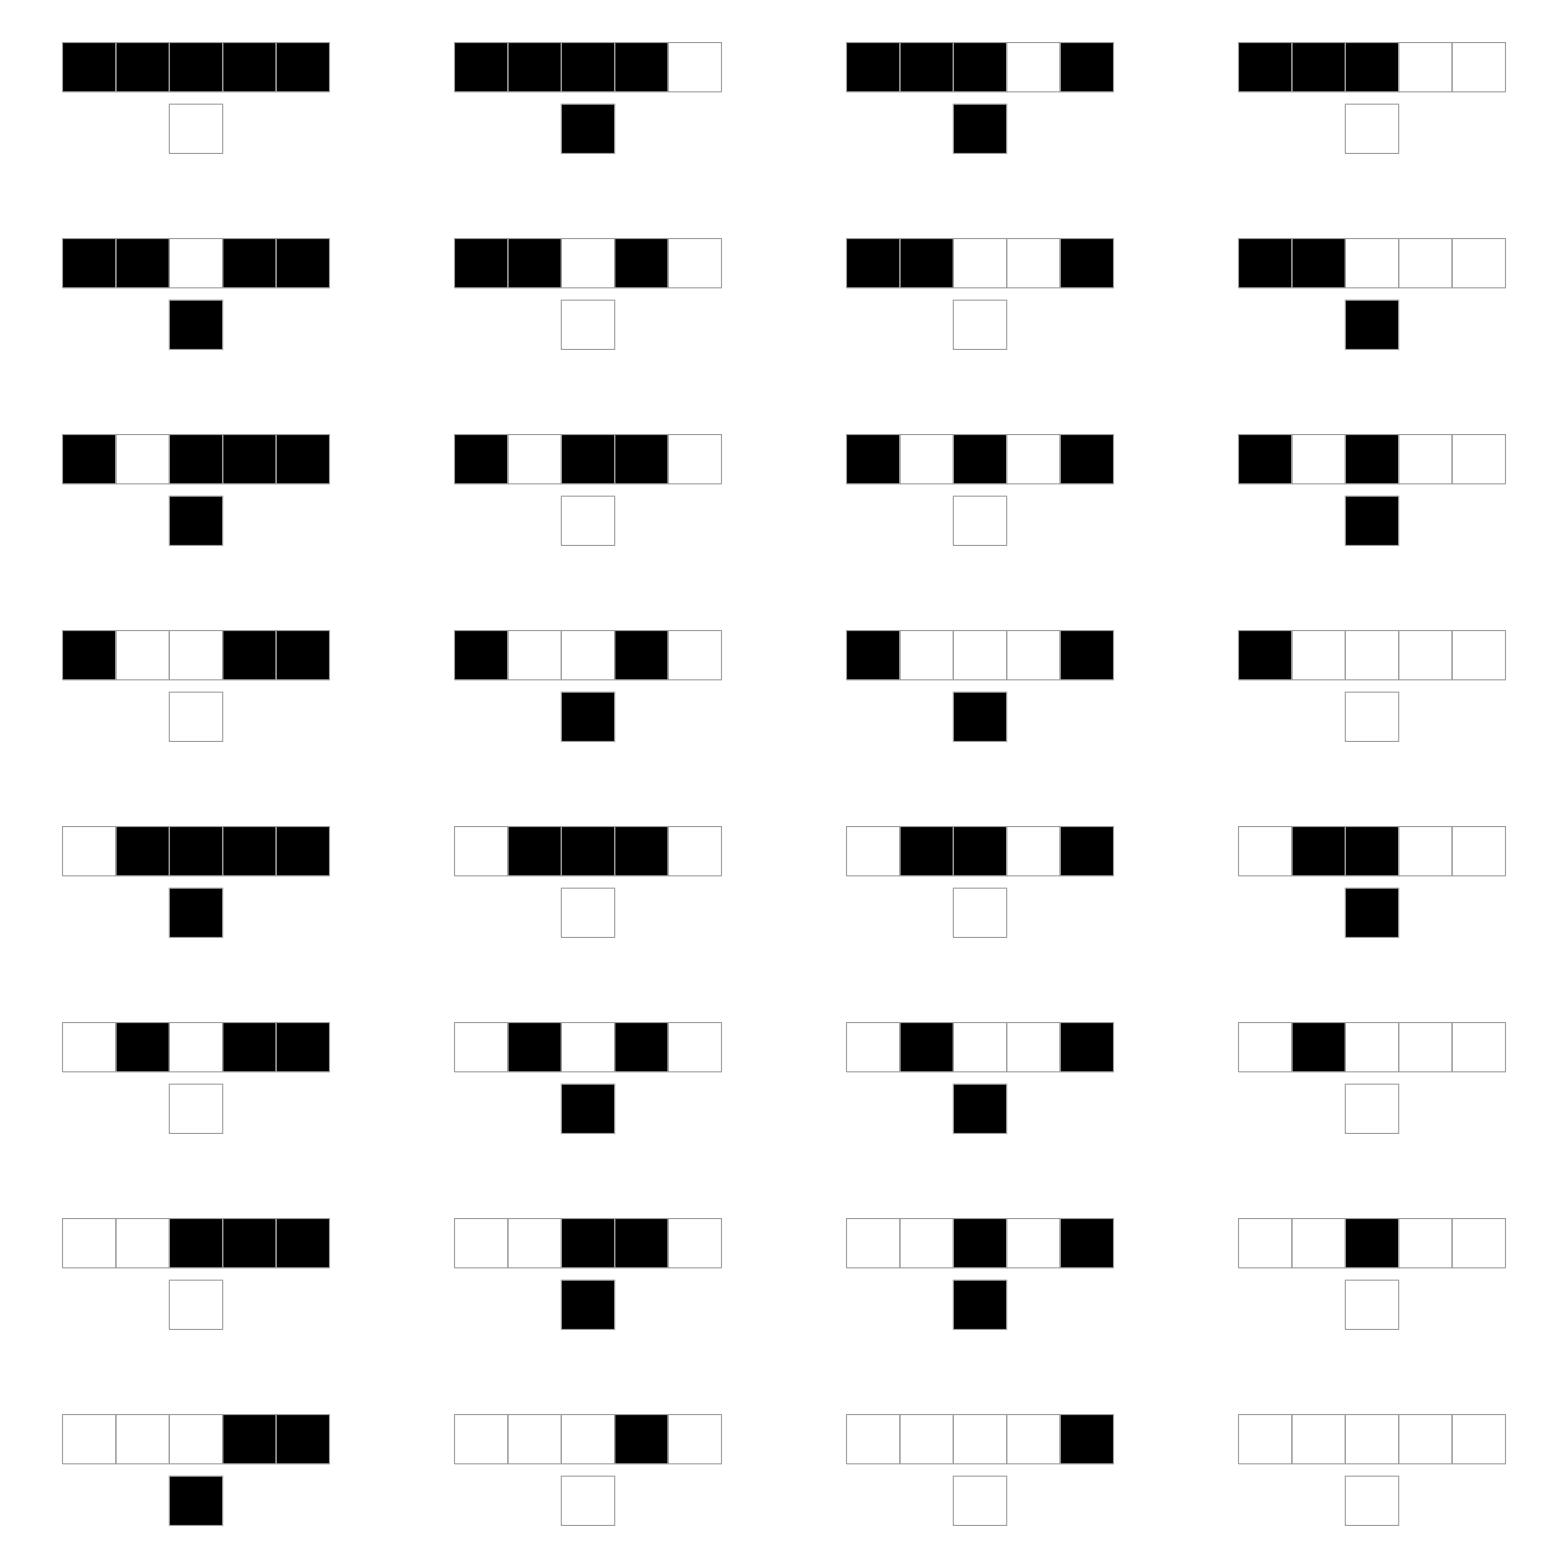

```mathematica
RulePlot[CellularAutomaton[{1771476584, 2, 2}]]
```

```mathematica
X^(Y&~X)^(Z& (~X^(Y&X)))
```

```mathematica
Xor[Xor[x, And[y, Not[x]]], And[z, Xor[Not[x], And[y, x]]]]
```

```mathematica
x⊻(y&&!x)⊻(z&&((y&&x)⊻!x))//v
```

14

```mathematica
v=(VertexCount@*ExpressionTree)
```

VertexCount@*ExpressionTree

```mathematica
Simplify[x⊻(y&&!x)⊻(z&&((y&&x)⊻!x))]
```

```mathematica
(x||y||z)&&!(y&&z)//v
```

9

```mathematica
BooleanFunction[x⊻(y&&!x)⊻(z&&((y&&x)⊻!x))]
```

BooleanFunction::bspec: BooleanFunction[x⊻(y&&!x)⊻(z&&((y&&x)⊻!x))] is not a valid BooleanFunction specification.

BooleanFunction[x⊻(y&&!x)⊻(z&&((y&&x)⊻!x))]

```mathematica
f[x_, y_, z_]:=x⊻(y&&!x)⊻(z&&((y&&x)⊻!x))
```

```mathematica
BooleanFunction[f@@@Tuples[{False, True}, 3]]
```

BooleanFunction[…]

```mathematica
b=BooleanFunction[…];
```

```mathematica
BooleanMinimize[b, "CNF"]@@{x, y, z}//Simplify//v
```

10

```mathematica
BooleanMinimize[b, "CNF"]//First//Simplify
```

!(#1&&#2&&#3)&&(#2||#3)

```mathematica
GPUStructureSearch[{1329, {3, 1}, 1}, 0, 1000000]
```

{400,1199,1211,3130,3398,3554,7199,7772,9571,9934,10420,11417,11573,12146,12607,20321,21355,22234,22960,23056,25000,25243,25729,32476,37636,38411,38444,38465,38471,38480,38486,38498,38519,38525,59687,59992,60416,61450,61693,61718,61874,62908,66067,66248,66553,66821,67282,68740,70441,70466,70622,70927,71170,71195,71656,74815,75301,85750,85931,86660,88423,88691,88847,90149,90305,90878,93040,93221,93526,94498,94679,94984,95252,95408,97114,97171,97357,97414,97427,97439,100816,101059,101084,101240,101813,101969,102274,103271,103427,103732,103975,104000,104461,105614,105919,106343,107801,108349,108374,108530,108835,109807,109832,109988,110293,110536,110561,112175,112723,113209,114362,114935,115091,115220,115223,115226,115268,115274,115283,115298,115307,115313,115316,115334,115361,115367,115396,115397,115421,115436,115451,115466,115475,115478,115496,115502,115529,115577,177785,179548,180520,181006,181978,184165,184315,184651,185075,186377,186533,186838,188539,189025,189268,190907,191212,191455,191480,191941,192938,193094,193667,193823,194128,194495,194513,195125,195281,195586,195829,196028,197287,197773,200203,201686,201842,202147,202390,202876,205792,206035,206216,206789,206945,208247,208403,208976,209437,211163,212621,214178,214196,214783,215269,215512,215998,218185,223531,224285,225475,225743,229120,230273,230846,232304,233494,235394,250261,250504,250990,257065,257551,259009,260710,260735,260891,264841,266113,274318,274561,284524,288169,289141,289627,290051,291085,291341,291509,292000,292057,292070,292082,292238,292543,293515,293540,293696,294001,294244,294269,294730,295883,296456,296612,302263,302749,303173,304631,306637,307123,307366,307852,310768,311036,311740,312226,313198,313684,313927,314413,315385,315871,318326,318482,319784,319940,320245,320488,320974,322856,323890,324314,324862,325348,326320,326806,327049,327535,328507,328688,328993,329261,330451,330719,331423,331909,332906,333062,333367,333610,341810,342383,342539,343841,343997,344570,344726,345644,345650,345653,345662,345665,345668,345674,345686,345689,345695,345698,345704,345707,345794,345806,345812,345824,345836,345842,345857,345860,345866,345869,345902,345941,345944,345947,345956,345968,345974,345977,345986,345992,345995,346001,346003,346004,346010,346013,346016,346019,346022,346028,346031,346103,346109,346118,346136,346139,346148,346154,346157,346163,346166,346172,346175,346181,346184,346187,346190,346193,346199,346211,346217,346220,346229,346235,346238,346241,346244,346246,346253,346256,346262,346265,346271,346274,346292,346310,346319,346325,346340,346343,346346,346349,346352,346354,346355,346361,346376,346403,346409,346427,346430,346433,346442,346448,346472,346478,346481,346487,346490,346496,346499,346505,346508,346514,346517,346523,346529,346535,346538,346544,346565,346571,346589,346595,346604,346634,346640,346643,346649,346652,346658,346661,346667,346670,346676,346679,346685,346697,346703,346706,346715,346721,346724,346730,346732,346733,346739,346742,346745,346748,346751,346757,346760,348371,348944,350402,353492,532652,534266,541375,541400,541556,541861,546964,547207,547232,547693,547936,549394,550609,554254,554497,560815,569102,569258,572018,574666,576124,576367,576853,579769,592162,595321,597994,598237,598723,601882,601907,602063,602368,602611,602636,611540,617945,618406,628151,628307,628880,636874,637360,637628,639086,642463,645622,646108,646351,651940,652364,653398,654856,655099,655585,657286,658769,658925,660931,660956,661112,661417,661660,661685,662146,663299,665062,665330,665486,666034,666059,666215,666520,667492,667517,667673,667978,668221,668246,668707,670433,670589,670894,671891,672352,674807,676421,676726,676969,676994,678184,678913,679181,679337,680639,680795,681368,683530,683711,684016,684988,685169,685474,685742,685898,687175,687929,688390,689362,689543,690116,690577,691574,691730,694490,696104,697138,697867,698596,698864,699020,700297,700783,701026,703213,703394,703699,704852,705425,705581,706883,707039,707612,749140,750598,750623,750779,756916,760561,764935,768848,770767,771035,771191,772493,772649,773222,774836,775565,777571,777596,777752,778057,783403,783889,789721,792176,792332,792905,794338,794519,795248,797254,797279,797435,797740,798712,798737,798893,799198,799441,799466,799927,801385,801653,801809,802843,803111,803267,803815,803840,803996,804301,805273,805298,805454,806488,807946,808214,809404,809672,809828,810862,812320,812563,812588,813049,814202,816937,816962,817118,817423,818395,818420,818576,818881,819124,819149,820582,821068,821336,821492,824956,824981,825137,825442,825685,825710,826171,830084,830240,833704,833885,834190,835648,836072,838078,838103,838259,838564,838807,838832,839293,841019,842209,842477,842633,843181,843206,843362,843667,844639,844664,844820,845125,845368,845393,845854,846826,847312,847580,848770,849038,849767,849923,851686,851929,851954,852415,853387,853568,854297,856303,856328,856484,856789,857761,857786,857942,858247,858490,858515,858976,859948,860434,860702,860858,861892,862160,862316,862864,862889,863045,863350,866995,868453,869450,869606,869911,870908,871064,871369,871612,872098,873556,875929,875986,875999,876011,876167,876472,877444,877930,878173,878659,880117,880385,881575,881843,882547,883033,884005,884491,884734,885220,886192,886678,891052,891295,891320,891781,899314,899800,900224,901258,901501,901987,902230,903688,904442,904903,908548,908791,912617,912922,914380,924125,925558,926287,926312,932848,934306,946456,948643,949615,952288,952531,953017,964924,966139,966868,967111,967136,971666,972395,973672,983174,987280,991897,993355,997910,998483,998639,999941,2627786,20990041,27598819,44789059,35447360707,525304562024518979,880853240277422984}

```mathematica
ParallelMap[ClickToCopy[AArrayPlot[{1329, {3, 1}, 1}, #, 1000], #]&,[[;;UpTo[50]]]]
```

{-Graphics-400,-Graphics-1199,-Graphics-1211,-Graphics-3130,-Graphics-3398,-Graphics-3554,-Graphics-7199,-Graphics-7772,-Graphics-9571,-Graphics-9934,-Graphics-10420,-Graphics-11417,-Graphics-11573,-Graphics-12146,-Graphics-12607,-Graphics-20321,-Graphics-21355,-Graphics-22234,-Graphics-22960,-Graphics-23056,-Graphics-25000,-Graphics-25243,-Graphics-25729,-Graphics-32476,-Graphics-37636,-Graphics-38411,-Graphics-38444,-Graphics-38465,-Graphics-38471,-Graphics-38480,-Graphics-38486,-Graphics-38498,-Graphics-38519,-Graphics-38525,-Graphics-59687,-Graphics-59992,-Graphics-60416,-Graphics-61450,-Graphics-61693,-Graphics-61718,-Graphics-61874,-Graphics-62908,-Graphics-66067,-Graphics-66248,-Graphics-66553,-Graphics-66821,-Graphics-67282,-Graphics-68740,-Graphics-70441,-Graphics-70466}

```mathematica
AArrayPlot[{1329, {3, 1}, 1}, 38411, 2000]
```

-Graphics-

```mathematica
AArrayPlot[{13, {2, 1}, 2}, Join[IntegerDigits[189, 2], {0, 0, 0, 0, 0, 0, 0}, IntegerDigits[187, 2]], Frame->False]
```

```mathematica
AArrayPlot[{20, {2, 1}, 2}, Join[IntegerDigits[189, 2], {0, 0, 0, 0, 0, 0, 0}, IntegerDigits[187, 2]], Frame->False]
```

-Graphics-

```mathematica
AArrayPlot[{20, {2, 1}, 2}, Join[{0,0,0,0,0,0,0,1,1,1,1,1,0,0,0,0,1,1,1,1,1,0,0,0,0,0,0,0}, {0}, {0,0,1,1,0,0,0,0,0,1,1,0,0,0,0,0,0,1,1,0,0,0,0,0,1,1,0,0}], Frame->False]
```

-Graphics-

```mathematica
MinimalBooleanForm[BooleanFunction[30]]
```

(#3&&!#2)⊻#1⊻#2

```mathematica
bf=BooleanFunction[30]
```

BooleanFunction[…]

```mathematica
bf[bf[#1, #2, #3], bf[#2, #3, #4], bf[#4, #5, #6]]&@@@Tuples[{False, True}, 9]
```

{False,False,False,False,False,False,False,False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

## Newer Stuff

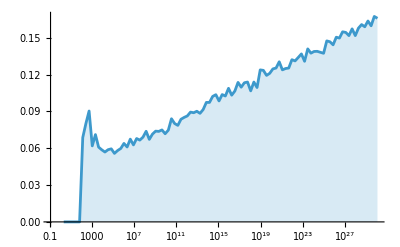

```mathematica
Clear[IsPersistent];
IsPersistent[init_]:=Unitize[Total[CellularAutomaton[{20, {2, 1}, 2},{IntegerDigits[init, 2], 0}, {{{1000}}}]]]

IsItself[init_]:=Length[DetectPeriod[{20, {2, 1}, 2}, init]]==1

IsBoth[init_]:=Boole[(IsPersistent[init]==1)&&IsItself[init]]

FrequencyOf[func_, min_, max_, n_]:=N[Total[ParallelMap[func, RandomInteger[{min, max}, n]]]]/n

res=ProgressMap[{2^#, FrequencyOf[IsBoth, 2^#, 2^(#+1), 10000]}&, Range[100]];

ListLogLinearPlot[res, Joined->True,  Filling->Axis]
```

```mathematica
AArrayPlot[{216, {2, 1}, 3}, RandomInteger[10^5]]
```

-Graphics-

```mathematica
AArrayPlot[{20, {2, 1}, 2}, RandomInteger[10^20], 50, Frame->False]
```

-Graphics-

```mathematica
res
```

{{2,0.},{4,0.},{8,0.},{16,0.},{32,0.},{64,0.},{128,0.0687},{256,0.0802},{512,0.0903},{1024,0.0619},{2048,0.0711},{4096,0.0609},{8192,0.0587},{16384,0.0569},{32768,0.0588},{65536,0.0595},{131072,0.0558},{262144,0.0581},{524288,0.0598},{1048576,0.0639},{2097152,0.061},{4194304,0.0674},{8388608,0.0627},{16777216,0.0679},{33554432,0.0666},{67108864,0.069},{134217728,0.0738},{268435456,0.0672},{536870912,0.0715},{1073741824,0.0739},{2147483648,0.0737},{4294967296,0.0749},{8589934592,0.0718},{17179869184,0.0747},{34359738368,0.084},{68719476736,0.0801},{137438953472,0.0786},{274877906944,0.0836},{549755813888,0.0851},{1099511627776,0.0863},{2199023255552,0.0894},{4398046511104,0.0889},{8796093022208,0.0901},{17592186044416,0.0884},{35184372088832,0.0915},{70368744177664,0.0973},{140737488355328,0.0973},{281474976710656,0.1022},{562949953421312,0.1036},{1125899906842624,0.0985},{2251799813685248,0.1037},{4503599627370496,0.1025},{9007199254740992,0.1088},{18014398509481984,0.1032},{36028797018963968,0.1066},{72057594037927936,0.1136},{144115188075855872,0.1097},{288230376151711744,0.1133},{576460752303423488,0.1139},{1152921504606846976,0.1067},{2305843009213693952,0.1139},{4611686018427387904,0.1094},{9223372036854775808,0.1238},{18446744073709551616,0.1234},{36893488147419103232,0.1193},{73786976294838206464,0.121},{147573952589676412928,0.1246},{295147905179352825856,0.1253},{590295810358705651712,0.1304},{1180591620717411303424,0.1238},{2361183241434822606848,0.1249},{4722366482869645213696,0.1253},{9444732965739290427392,0.1321},{18889465931478580854784,0.1311},{37778931862957161709568,0.1339},{75557863725914323419136,0.1368},{151115727451828646838272,0.1308},{302231454903657293676544,0.1409},{604462909807314587353088,0.1374},{1208925819614629174706176,0.1388},{2417851639229258349412352,0.1389},{4835703278458516698824704,0.1381},{9671406556917033397649408,0.1373},{19342813113834066795298816,0.1474},{38685626227668133590597632,0.1467},{77371252455336267181195264,0.1442},{154742504910672534362390528,0.1504},{309485009821345068724781056,0.1497},{618970019642690137449562112,0.1548},{1237940039285380274899124224,0.1543},{2475880078570760549798248448,0.1517},{4951760157141521099596496896,0.1572},{9903520314283042199192993792,0.1517},{19807040628566084398385987584,0.1578},{39614081257132168796771975168,0.1607},{79228162514264337593543950336,0.1589},{158456325028528675187087900672,0.1636},{316912650057057350374175801344,0.1597},{633825300114114700748351602688,0.1673},{1267650600228229401496703205376,0.1658}}

```mathematica
r=RandomInteger[10^24];
AArrayPlot[{20, {2, 1}, 2}, r]
IsBoth[r]
```

-Graphics-

0

```mathematica
RandomSample[{0, 0, 4, 0, 8, 4, 0, 4, 0}, 9]
```

{0,0,4,0,0,4,8,0,4}

```mathematica
-Graphics-[[0]]
```

Graphics

```mathematica
List@@-Graphics-
```

{{{},{{{},{},{Hue[0.67, 0.6, 0.6],Directive[PointSize[1/60],RGBColor[0.24, 0.6, 0.8],AbsoluteThickness[2]],Line[{{1.,0.},{2.,0.},{3.,0.},{4.,0.},{5.,0.},{6.,0.},{7.,0.},{8.,0.},{9.,0.},{10.,0.01},{11.,0.01},{12.,0.},{13.,0.},{14.,0.01},{15.,0.02},{16.,0.02},{17.,0.04},{18.,0.02},{19.,0.01},{20.,0.06},{21.,0.02},{22.,0.},{23.,0.07},{24.,0.07},{25.,0.03},{26.,0.05},{27.,0.03},{28.,0.07},{29.,0.02},{30.,0.03},{31.,0.07},{32.,0.05},{33.,0.04},{34.,0.08},{35.,0.07},{36.,0.07},{37.,0.1},{38.,0.06},{39.,0.07},{40.,0.08},{41.,0.15},{42.,0.09},{43.,0.08},{44.,0.09},{45.,0.12},{46.,0.12},{47.,0.1},{48.,0.07},{49.,0.09},{50.,0.09},{51.,0.13},{52.,0.06},{53.,0.09},{54.,0.04},{55.,0.15},{56.,0.07},{57.,0.07},{58.,0.11},{59.,0.09},{60.,0.07},{61.,0.05},{62.,0.13},{63.,0.13},{64.,0.11},{65.,0.13},{66.,0.1},{67.,0.07},{68.,0.07},{69.,0.09},{70.,0.06},{71.,0.09},{72.,0.08},{73.,0.12},{74.,0.05},{75.,0.04},{76.,0.1375},{77.,0.0588235},{78.,0.0638298},{79.,0.},{80.,0.0526316},{81.,0.},{82.,0.0666667},{83.,0.},{84.,0.},{85.,0.},{86.,0.},{87.,0.}}]}}},{{},{}}},AspectRatio→1/GoldenRatio,Axes→{True,True},AxesLabel→{None,None},AxesOrigin→{0.,0},DefaultBaseStyle→{PlotGraphics,Graphics},DisplayFunction→Identity,Frame→{{False,False},{False,False}},FrameLabel→{{None,None},{None,None}},FrameTicks→{{Automatic,Automatic},{Automatic,Automatic}},GridLines→{None,None},GridLinesStyle→Directive[GrayLevel[0.5, 0.4]],ImageSize→{676.667,Automatic},Method→{AxisPadding→Scaled[0.02],DefaultBoundaryStyle→Automatic,DefaultGraphicsInteraction→{Version→1.2,TrackMousePosition→{True,False},Effects→{Highlight→{ratio→2},HighlightPoint→{ratio→2},Droplines→{freeformCursorMode→True,placement→{x→All,y→None}}}},DefaultMeshStyle→AbsolutePointSize[6],DefaultPlotStyle→{Directive[RGBColor[0.24, 0.6, 0.8],AbsoluteThickness[2]],Directive[RGBColor[0.95, 0.627, 0.1425],AbsoluteThickness[2]],Directive[RGBColor[0.455, 0.7, 0.21],AbsoluteThickness[2]],Directive[RGBColor[0.922526, 0.385626, 0.209179],AbsoluteThickness[2]],Directive[RGBColor[0.578, 0.51, 0.85],AbsoluteThickness[2]],Directive[RGBColor[0.772079, 0.431554, 0.102387],AbsoluteThickness[2]],Directive[RGBColor[0., 0.6, 0.6],AbsoluteThickness[2]],Directive[RGBColor[0.9, 0.36, 0.684],AbsoluteThickness[2]],Directive[RGBColor[0.56, 0.7, 0.],AbsoluteThickness[2]],Directive[RGBColor[0.9, 0.54, 0.],AbsoluteThickness[2]],Directive[RGBColor[0.585, 0.5976, 0.9],AbsoluteThickness[2]],Directive[RGBColor[0.9, 0.45, 0.45],AbsoluteThickness[2]],Directive[RGBColor[0.7632186717367253, 0.8174402144034898, 0.],AbsoluteThickness[2]],Directive[RGBColor[0.8554632469481959, 0.24885384718327969, 0.833405387394855],AbsoluteThickness[2]],Directive[RGBColor[0.032972823413648836, 0.7396719749139476, 0.534700104525218],AbsoluteThickness[2]]},DomainPadding→Scaled[0.02],RangePadding→Scaled[0.05],OptimizePlotMarkers→True,IncludeHighlighting→Automatic,HighlightStyle→Automatic,OptimizePlotMarkers→True,IncludeHighlighting→CurrentSet,HighlightStyle→Automatic,OptimizePlotMarkers→True,CoordinatesToolOptions→{DisplayFunction→({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&),CopiedValueFunction→({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&)}},PlotInteractivity:>True,PlotRange→{{0.,90.},{0,0.15}},PlotRangeClipping→True,PlotRangePadding→{{Scaled[0.02],Scaled[0.02]},{Scaled[0.02],Scaled[0.05]}},Ticks→{Automatic,Automatic}}

```mathematica
Join[%, {PlotRange->{{0, 128}, Automatic}}]
```

```mathematica
{{{},{{{},{},{Hue[0.67, 0.6, 0.6],Directive[PointSize[1/60],RGBColor[0.24, 0.6, 0.8],AbsoluteThickness[2]],Line[{{1.,0.},{2.,0.},{3.,0.},{4.,0.},{5.,0.},{6.,0.},{7.,0.},{8.,0.},{9.,0.},{10.,0.01},{11.,0.01},{12.,0.},{13.,0.},{14.,0.01},{15.,0.02},{16.,0.02},{17.,0.04},{18.,0.02},{19.,0.01},{20.,0.06},{21.,0.02},{22.,0.},{23.,0.07},{24.,0.07},{25.,0.03},{26.,0.05},{27.,0.03},{28.,0.07},{29.,0.02},{30.,0.03},{31.,0.07},{32.,0.05},{33.,0.04},{34.,0.08},{35.,0.07},{36.,0.07},{37.,0.1},{38.,0.06},{39.,0.07},{40.,0.08},{41.,0.15},{42.,0.09},{43.,0.08},{44.,0.09},{45.,0.12},{46.,0.12},{47.,0.1},{48.,0.07},{49.,0.09},{50.,0.09},{51.,0.13},{52.,0.06},{53.,0.09},{54.,0.04},{55.,0.15},{56.,0.07},{57.,0.07},{58.,0.11},{59.,0.09},{60.,0.07},{61.,0.05},{62.,0.13},{63.,0.13},{64.,0.11},{65.,0.13},{66.,0.1},{67.,0.07},{68.,0.07},{69.,0.09},{70.,0.06},{71.,0.09},{72.,0.08},{73.,0.12},{74.,0.05},{75.,0.04},{76.,0.1375},{77.,0.058823529411764705},{78.,0.06382978723404255},{79.,0.},{80.,0.05263157894736842},{81.,0.},{82.,0.06666666666666667},{83.,0.},{84.,0.},{85.,0.},{86.,0.},{87.,0.}}]}}},{{},{}}},AspectRatio->1/GoldenRatio,Axes->{True,True},AxesLabel->{None,None},AxesOrigin->{0.,0},DefaultBaseStyle->{"PlotGraphics","Graphics"},DisplayFunction->Identity,Frame->{{False,False},{False,False}},FrameLabel->{{None,None},{None,None}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},GridLines->{None,None},GridLinesStyle->Directive[GrayLevel[0.5, 0.4]],ImageSize->{676.6666666666667,Automatic},Method->{"AxisPadding"->Scaled[0.02],"DefaultBoundaryStyle"->Automatic,"DefaultGraphicsInteraction"->{"Version"->1.2,"TrackMousePosition"->{True,False},"Effects"->{"Highlight"->{"ratio"->2},"HighlightPoint"->{"ratio"->2},"Droplines"->{"freeformCursorMode"->True,"placement"->{"x"->"All","y"->"None"}}}},"DefaultMeshStyle"->AbsolutePointSize[6],"DefaultPlotStyle"->{Directive[RGBColor[0.24, 0.6, 0.8],AbsoluteThickness[2]],Directive[RGBColor[0.95, 0.627, 0.1425],AbsoluteThickness[2]],Directive[RGBColor[0.455, 0.7, 0.21],AbsoluteThickness[2]],Directive[RGBColor[0.922526, 0.385626, 0.209179],AbsoluteThickness[2]],Directive[RGBColor[0.578, 0.51, 0.85],AbsoluteThickness[2]],Directive[RGBColor[0.772079, 0.431554, 0.102387],AbsoluteThickness[2]],Directive[RGBColor[0., 0.6, 0.6],AbsoluteThickness[2]],Directive[RGBColor[0.9, 0.36, 0.684],AbsoluteThickness[2]],Directive[RGBColor[0.56, 0.7, 0.],AbsoluteThickness[2]],Directive[RGBColor[0.9, 0.54, 0.],AbsoluteThickness[2]],Directive[RGBColor[0.585, 0.5976, 0.9],AbsoluteThickness[2]],Directive[RGBColor[0.9, 0.45, 0.45],AbsoluteThickness[2]],Directive[RGBColor[0.7632186717367253, 0.8174402144034898, 0.],AbsoluteThickness[2]],Directive[RGBColor[0.8554632469481959, 0.24885384718327969, 0.833405387394855],AbsoluteThickness[2]],Directive[RGBColor[0.032972823413648836, 0.7396719749139476, 0.534700104525218],AbsoluteThickness[2]]},"DomainPadding"->Scaled[0.02],"RangePadding"->Scaled[0.05],"OptimizePlotMarkers"->True,"IncludeHighlighting"->Automatic,"HighlightStyle"->Automatic,"OptimizePlotMarkers"->True,"IncludeHighlighting"->"CurrentSet","HighlightStyle"->Automatic,"OptimizePlotMarkers"->True,"CoordinatesToolOptions"->{"DisplayFunction"->({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&),"CopiedValueFunction"->({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&)}},PlotInteractivity:>True,PlotRange->{{0.,128.},{0,0.15}},PlotRangeClipping->True,PlotRangePadding->{{Scaled[0.02],Scaled[0.02]},{Scaled[0.02],Scaled[0.05]}},Ticks->{Automatic,Automatic}}
```

```mathematica
{{{},{{{},{},{Hue[0.67, 0.6, 0.6],Directive[PointSize[1/60],RGBColor[0.24, 0.6, 0.8],AbsoluteThickness[2]],Line[{{1.,0.},{2.,0.},{3.,0.},{4.,0.},{5.,0.},{6.,0.},{7.,0.},{8.,0.},{9.,0.},{10.,0.01},{11.,0.01},{12.,0.},{13.,0.},{14.,0.01},{15.,0.02},{16.,0.02},{17.,0.04},{18.,0.02},{19.,0.01},{20.,0.06},{21.,0.02},{22.,0.},{23.,0.07},{24.,0.07},{25.,0.03},{26.,0.05},{27.,0.03},{28.,0.07},{29.,0.02},{30.,0.03},{31.,0.07},{32.,0.05},{33.,0.04},{34.,0.08},{35.,0.07},{36.,0.07},{37.,0.1},{38.,0.06},{39.,0.07},{40.,0.08},{41.,0.15},{42.,0.09},{43.,0.08},{44.,0.09},{45.,0.12},{46.,0.12},{47.,0.1},{48.,0.07},{49.,0.09},{50.,0.09},{51.,0.13},{52.,0.06},{53.,0.09},{54.,0.04},{55.,0.15},{56.,0.07},{57.,0.07},{58.,0.11},{59.,0.09},{60.,0.07},{61.,0.05},{62.,0.13},{63.,0.13},{64.,0.11},{65.,0.13},{66.,0.1},{67.,0.07},{68.,0.07},{69.,0.09},{70.,0.06},{71.,0.09},{72.,0.08},{73.,0.12},{74.,0.05},{75.,0.04},{76.,0.1375},{77.,0.058823529411764705},{78.,0.06382978723404255},{79.,0.},{80.,0.05263157894736842},{81.,0.},{82.,0.06666666666666667},{83.,0.},{84.,0.},{85.,0.},{86.,0.},{87.,0.}, {127., 0.}}]}}},{{},{}}},AspectRatio->1/GoldenRatio,Axes->{True,True},AxesLabel->{None,None},AxesOrigin->{0.,0},DefaultBaseStyle->{"PlotGraphics","Graphics"},DisplayFunction->Identity,Frame->{{False,False},{False,False}},FrameLabel->{{None,None},{None,None}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},GridLines->{None,None},GridLinesStyle->Directive[GrayLevel[0.5, 0.4]],ImageSize->{676.6666666666667,Automatic},Method->{"AxisPadding"->Scaled[0.02],"DefaultBoundaryStyle"->Automatic,"DefaultGraphicsInteraction"->{"Version"->1.2,"TrackMousePosition"->{True,False},"Effects"->{"Highlight"->{"ratio"->2},"HighlightPoint"->{"ratio"->2},"Droplines"->{"freeformCursorMode"->True,"placement"->{"x"->"All","y"->"None"}}}},"DefaultMeshStyle"->AbsolutePointSize[6],"DefaultPlotStyle"->{Directive[RGBColor[0.24, 0.6, 0.8],AbsoluteThickness[2]],Directive[RGBColor[0.95, 0.627, 0.1425],AbsoluteThickness[2]],Directive[RGBColor[0.455, 0.7, 0.21],AbsoluteThickness[2]],Directive[RGBColor[0.922526, 0.385626, 0.209179],AbsoluteThickness[2]],Directive[RGBColor[0.578, 0.51, 0.85],AbsoluteThickness[2]],Directive[RGBColor[0.772079, 0.431554, 0.102387],AbsoluteThickness[2]],Directive[RGBColor[0., 0.6, 0.6],AbsoluteThickness[2]],Directive[RGBColor[0.9, 0.36, 0.684],AbsoluteThickness[2]],Directive[RGBColor[0.56, 0.7, 0.],AbsoluteThickness[2]],Directive[RGBColor[0.9, 0.54, 0.],AbsoluteThickness[2]],Directive[RGBColor[0.585, 0.5976, 0.9],AbsoluteThickness[2]],Directive[RGBColor[0.9, 0.45, 0.45],AbsoluteThickness[2]],Directive[RGBColor[0.7632186717367253, 0.8174402144034898, 0.],AbsoluteThickness[2]],Directive[RGBColor[0.8554632469481959, 0.24885384718327969, 0.833405387394855],AbsoluteThickness[2]],Directive[RGBColor[0.032972823413648836, 0.7396719749139476, 0.534700104525218],AbsoluteThickness[2]]},"DomainPadding"->Scaled[0.02],"RangePadding"->Scaled[0.05],"OptimizePlotMarkers"->True,"IncludeHighlighting"->Automatic,"HighlightStyle"->Automatic,"OptimizePlotMarkers"->True,"IncludeHighlighting"->"CurrentSet","HighlightStyle"->Automatic,"OptimizePlotMarkers"->True,"CoordinatesToolOptions"->{"DisplayFunction"->({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&),"CopiedValueFunction"->({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&)}},PlotInteractivity:>True,PlotRange->{{0.,128.},{0,0.15}},PlotRangeClipping->True,PlotRangePadding->{{Scaled[0.02],Scaled[0.02]},{Scaled[0.02],Scaled[0.05]}},Ticks->{Automatic,Automatic}}
```

```mathematica
{{{},{{{},{},{Hue[0.67, 0.6, 0.6],Directive[PointSize[1/60],RGBColor[0.24, 0.6, 0.8],AbsoluteThickness[2]],Line[{{1.,0.},{2.,0.},{3.,0.},{4.,0.},{5.,0.},{6.,0.},{7.,0.},{8.,0.},{9.,0.},{10.,0.01},{11.,0.01},{12.,0.},{13.,0.},{14.,0.01},{15.,0.02},{16.,0.02},{17.,0.04},{18.,0.02},{19.,0.01},{20.,0.06},{21.,0.02},{22.,0.},{23.,0.07},{24.,0.07},{25.,0.03},{26.,0.05},{27.,0.03},{28.,0.07},{29.,0.02},{30.,0.03},{31.,0.07},{32.,0.05},{33.,0.04},{34.,0.08},{35.,0.07},{36.,0.07},{37.,0.1},{38.,0.06},{39.,0.07},{40.,0.08},{41.,0.15},{42.,0.09},{43.,0.08},{44.,0.09},{45.,0.12},{46.,0.12},{47.,0.1},{48.,0.07},{49.,0.09},{50.,0.09},{51.,0.13},{52.,0.06},{53.,0.09},{54.,0.04},{55.,0.15},{56.,0.07},{57.,0.07},{58.,0.11},{59.,0.09},{60.,0.07},{61.,0.05},{62.,0.13},{63.,0.13},{64.,0.11},{65.,0.13},{66.,0.1},{67.,0.07},{68.,0.07},{69.,0.09},{70.,0.06},{71.,0.09},{72.,0.08},{73.,0.12},{74.,0.05},{75.,0.04},{76.,0.1375},{77.,0.058823529411764705},{78.,0.06382978723404255},{79.,0.},{80.,0.05263157894736842},{81.,0.},{82.,0.06666666666666667},{83.,0.},{84.,0.},{85.,0.},{86.,0.},{87.,0.}}]}}},{{},{}}},AspectRatio->1/GoldenRatio,Axes->{True,True},AxesLabel->{None,None},AxesOrigin->{0.,0},DefaultBaseStyle->{"PlotGraphics","Graphics"},DisplayFunction->Identity,Frame->{{False,False},{False,False}},FrameLabel->{{None,None},{None,None}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},GridLines->{None,None},GridLinesStyle->Directive[GrayLevel[0.5, 0.4]],ImageSize->{676.6666666666667,Automatic},Method->{"AxisPadding"->Scaled[0.02],"DefaultBoundaryStyle"->Automatic,"DefaultGraphicsInteraction"->{"Version"->1.2,"TrackMousePosition"->{True,False},"Effects"->{"Highlight"->{"ratio"->2},"HighlightPoint"->{"ratio"->2},"Droplines"->{"freeformCursorMode"->True,"placement"->{"x"->"All","y"->"None"}}}},"DefaultMeshStyle"->AbsolutePointSize[6],"DefaultPlotStyle"->{Directive[RGBColor[0.24, 0.6, 0.8],AbsoluteThickness[2]],Directive[RGBColor[0.95, 0.627, 0.1425],AbsoluteThickness[2]],Directive[RGBColor[0.455, 0.7, 0.21],AbsoluteThickness[2]],Directive[RGBColor[0.922526, 0.385626, 0.209179],AbsoluteThickness[2]],Directive[RGBColor[0.578, 0.51, 0.85],AbsoluteThickness[2]],Directive[RGBColor[0.772079, 0.431554, 0.102387],AbsoluteThickness[2]],Directive[RGBColor[0., 0.6, 0.6],AbsoluteThickness[2]],Directive[RGBColor[0.9, 0.36, 0.684],AbsoluteThickness[2]],Directive[RGBColor[0.56, 0.7, 0.],AbsoluteThickness[2]],Directive[RGBColor[0.9, 0.54, 0.],AbsoluteThickness[2]],Directive[RGBColor[0.585, 0.5976, 0.9],AbsoluteThickness[2]],Directive[RGBColor[0.9, 0.45, 0.45],AbsoluteThickness[2]],Directive[RGBColor[0.7632186717367253, 0.8174402144034898, 0.],AbsoluteThickness[2]],Directive[RGBColor[0.8554632469481959, 0.24885384718327969, 0.833405387394855],AbsoluteThickness[2]],Directive[RGBColor[0.032972823413648836, 0.7396719749139476, 0.534700104525218],AbsoluteThickness[2]]},"DomainPadding"->Scaled[0.02],"RangePadding"->Scaled[0.05],"OptimizePlotMarkers"->True,"IncludeHighlighting"->Automatic,"HighlightStyle"->Automatic,"OptimizePlotMarkers"->True,"IncludeHighlighting"->"CurrentSet","HighlightStyle"->Automatic,"OptimizePlotMarkers"->True,"CoordinatesToolOptions"->{"DisplayFunction"->({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&),"CopiedValueFunction"->({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&)}},PlotInteractivity:>True,PlotRange->{{0.,128.},{0,0.15}},PlotRangeClipping->True,PlotRangePadding->{{Scaled[0.02],Scaled[0.02]},{Scaled[0.02],Scaled[0.05]}},Ticks->{Automatic,Automatic}}
```

{{{},{{{},{},{Hue[0.67, 0.6, 0.6],Directive[PointSize[1/60],RGBColor[0.24, 0.6, 0.8],AbsoluteThickness[2]],Line[{{1.,0.},{2.,0.},{3.,0.},{4.,0.},{5.,0.},{6.,0.},{7.,0.},{8.,0.},{9.,0.},{10.,0.01},{11.,0.01},{12.,0.},{13.,0.},{14.,0.01},{15.,0.02},{16.,0.02},{17.,0.04},{18.,0.02},{19.,0.01},{20.,0.06},{21.,0.02},{22.,0.},{23.,0.07},{24.,0.07},{25.,0.03},{26.,0.05},{27.,0.03},{28.,0.07},{29.,0.02},{30.,0.03},{31.,0.07},{32.,0.05},{33.,0.04},{34.,0.08},{35.,0.07},{36.,0.07},{37.,0.1},{38.,0.06},{39.,0.07},{40.,0.08},{41.,0.15},{42.,0.09},{43.,0.08},{44.,0.09},{45.,0.12},{46.,0.12},{47.,0.1},{48.,0.07},{49.,0.09},{50.,0.09},{51.,0.13},{52.,0.06},{53.,0.09},{54.,0.04},{55.,0.15},{56.,0.07},{57.,0.07},{58.,0.11},{59.,0.09},{60.,0.07},{61.,0.05},{62.,0.13},{63.,0.13},{64.,0.11},{65.,0.13},{66.,0.1},{67.,0.07},{68.,0.07},{69.,0.09},{70.,0.06},{71.,0.09},{72.,0.08},{73.,0.12},{74.,0.05},{75.,0.04},{76.,0.1375},{77.,0.0588235},{78.,0.0638298},{79.,0.},{80.,0.0526316},{81.,0.},{82.,0.0666667},{83.,0.},{84.,0.},{85.,0.},{86.,0.},{87.,0.}}]}}},{{},{}}},AspectRatio→1/GoldenRatio,Axes→{True,True},AxesLabel→{None,None},AxesOrigin→{0.,0},DefaultBaseStyle→{PlotGraphics,Graphics},DisplayFunction→Identity,Frame→{{False,False},{False,False}},FrameLabel→{{None,None},{None,None}},FrameTicks→{{Automatic,Automatic},{Automatic,Automatic}},GridLines→{None,None},GridLinesStyle→Directive[GrayLevel[0.5, 0.4]],ImageSize→{676.667,Automatic},Method→{AxisPadding→Scaled[0.02],DefaultBoundaryStyle→Automatic,DefaultGraphicsInteraction→{Version→1.2,TrackMousePosition→{True,False},Effects→{Highlight→{ratio→2},HighlightPoint→{ratio→2},Droplines→{freeformCursorMode→True,placement→{x→All,y→None}}}},DefaultMeshStyle→AbsolutePointSize[6],DefaultPlotStyle→{Directive[RGBColor[0.24, 0.6, 0.8],AbsoluteThickness[2]],Directive[RGBColor[0.95, 0.627, 0.1425],AbsoluteThickness[2]],Directive[RGBColor[0.455, 0.7, 0.21],AbsoluteThickness[2]],Directive[RGBColor[0.922526, 0.385626, 0.209179],AbsoluteThickness[2]],Directive[RGBColor[0.578, 0.51, 0.85],AbsoluteThickness[2]],Directive[RGBColor[0.772079, 0.431554, 0.102387],AbsoluteThickness[2]],Directive[RGBColor[0., 0.6, 0.6],AbsoluteThickness[2]],Directive[RGBColor[0.9, 0.36, 0.684],AbsoluteThickness[2]],Directive[RGBColor[0.56, 0.7, 0.],AbsoluteThickness[2]],Directive[RGBColor[0.9, 0.54, 0.],AbsoluteThickness[2]],Directive[RGBColor[0.585, 0.5976, 0.9],AbsoluteThickness[2]],Directive[RGBColor[0.9, 0.45, 0.45],AbsoluteThickness[2]],Directive[RGBColor[0.7632186717367253, 0.8174402144034898, 0.],AbsoluteThickness[2]],Directive[RGBColor[0.8554632469481959, 0.24885384718327969, 0.833405387394855],AbsoluteThickness[2]],Directive[RGBColor[0.032972823413648836, 0.7396719749139476, 0.534700104525218],AbsoluteThickness[2]]},DomainPadding→Scaled[0.02],RangePadding→Scaled[0.05],OptimizePlotMarkers→True,IncludeHighlighting→Automatic,HighlightStyle→Automatic,OptimizePlotMarkers→True,IncludeHighlighting→CurrentSet,HighlightStyle→Automatic,OptimizePlotMarkers→True,CoordinatesToolOptions→{DisplayFunction→({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&),CopiedValueFunction→({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&)}},PlotInteractivity:>True,PlotRange→{{0.,128.},{0,0.15}},PlotRangeClipping→True,PlotRangePadding→{{Scaled[0.02],Scaled[0.02]},{Scaled[0.02],Scaled[0.05]}},Ticks→{Automatic,Automatic}}

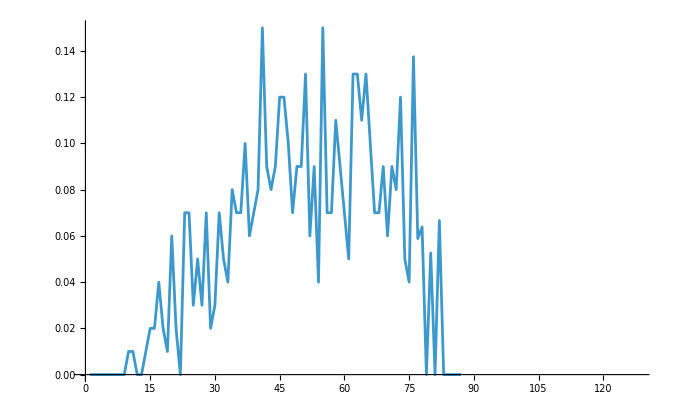

```mathematica
Graphics@@%
```

```mathematica
-Graphics-[[16]]
```

PlotRange→{{0.,90.},{0,0.15}}

{<|Rule→{20,{2,1},2},Canonical→189,Original→189,IsGliderGun→False,MaxDepth→0,MaxSteps→200,Period→1,Shift→0,LowestDepth→20|>,<|Rule→{20,{2,1},2},Canonical→635,Original→635,IsGliderGun→False,MaxDepth→0,MaxSteps→200,Period→1,Shift→1,LowestDepth→20|>,<|Rule→{20,{2,1},2},Canonical→151,Original→151,IsGliderGun→False,MaxDepth→0,MaxSteps→200,Period→2,Shift→0,LowestDepth→20|>,<|Rule→{20,{2,1},2},Canonical→595703,Original→595703,IsGliderGun→False,MaxDepth→0,MaxSteps→200,Period→4,Shift→0,LowestDepth→20|>,<|Rule→{20,{2,1},2},Canonical→610999,Original→610999,IsGliderGun→False,MaxDepth→0,MaxSteps→200,Period→4,Shift→0,LowestDepth→20|>,<|Rule→{20,{2,1},2},Canonical→187,Original→187,IsGliderGun→False,MaxDepth→0,MaxSteps→200,Period→9,Shift→1,LowestDepth→20|>,<|Rule→{20,{2,1},2},Canonical→15903,Original→195,IsGliderGun→False,MaxDepth→0,MaxSteps→200,Period→22,Shift→0,LowestDepth→20|>,<|Rule→{20,{2,1},2},Canonical→125231,Original→125231,IsGliderGun→False,MaxDepth→0,MaxSteps→200,Period→38,Shift→0,LowestDepth→20|>}